## Definitions

```mathematica
workdir=SetDirectory[NotebookDirectory[]];

listhisto={Joined->True,InterpolationOrder->0};

ListPlotH[list_,Label_,xlabel_,ylabel_,xmin_,xmax_,ymin_,ymax_,grids_,size_,addopt_]:=Module[{plot,options},
options=Union[{AxesOrigin->{xmin,ymin},Frame->True,PlotRange->{{xmin,xmax},{ymin,ymax}},GridLines->grids,GridLinesStyle->Dashed,ImageSize->size,BaseStyle->{FontFamily->"Arial",FontSize->size 0.03}},addopt];
plot=ListPlot[list,listhisto,options];
Return[plot]]

ListPlotG[list_,Label_,xmin_,xmax_,ymin_,ymax_,xdiv_,ydiv_,addopt_]:=Module[{plot,grids,options},
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options=Union[{AxesOrigin->{xmin,ymin},GridLines->grids,GridLinesStyle->Dashed,Frame->True,PlotLabel->Label,PlotRange->{{xmin,xmax},{ymin,ymax}}},addopt];
plot=ListPlot[list,options];
Return[plot]]

ListPlotHG[list_,Label_,xmin_,xmax_,ymin_,ymax_,xdiv_,ydiv_,addopt_]:=Module[{plot,grids,options},
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options=Union[{AxesOrigin->{xmin,ymin},GridLines->grids,GridLinesStyle->Dashed,Frame->True,PlotLabel->Label,PlotRange->{{xmin,xmax},{ymin,ymax}}},addopt];
plot=ListPlot[list,listhisto,options];
Return[plot]]

ListPlotHFG[list_,Label_,xmin_,xmax_,ymin_,ymax_,xdiv_,ydiv_,addopt_]:=Module[{plot,grids,options},
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options=Union[{AxesOrigin->{xmin,ymin},GridLines->grids,GridLinesStyle->Dashed,Frame->True,PlotLabel->Label,PlotRange->{{xmin,xmax},{ymin,ymax}}},addopt];
plot=ListPlot[list,listhisto,options];
Return[plot]]

ListLogPlotH[list_,Label_,xlabel_,ylabel_,xmin_,xmax_,ymin_,ymax_,grids_,size_,addopt_]:=Module[{plot,options},
options=Union[{AxesOrigin->{xmin,ymin},Frame->True,PlotRange->{{xmin,xmax},{ymin,ymax}},GridLines->grids,GridLinesStyle->Dashed,ImageSize->size,BaseStyle->{FontFamily->"Arial",FontSize->size 0.03}},addopt];
plot=ListLogPlot[list,listhisto,options];
Return[plot]]

ListLogPlotHG[list_,Label_,xmin_,xmax_,ymin_,ymax_,xdiv_,ydiv_,addopt_]:=Module[{plot,grids,options},
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options=Union[{AxesOrigin->{xmin,ymin},GridLines->grids,GridLinesStyle->Dashed,Frame->True,PlotLabel->Label,PlotRange->{{xmin,xmax},{ymin,ymax}}},addopt];
plot=ListLogPlot[list,listhisto,options];
Return[plot]]

PlotHG[Label_,path_,col1_,col2_,PP_,AP_,xmin_,xmax_,ymin_,ymax_,xdiv_,ydiv_]:=Module[{data,data2,data3,data4,plot,grids,options},
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options={AxesOrigin->{xmin,ymin},GridLines->grids,GridLinesStyle->Dashed,Frame->True,ImageSize->400,PlotLabel->Label,PlotRange->{{0,xmax},{0,ymax}}};
data=ReadList[path,Number,RecordLists->True];
data2={#[[col1]],#[[col2]]}&/@data;
data3=PrependTo[data2,{PP,0}];
data4=AppendTo[data3,{AP,0}];
plot=ListPlot[data4,listhisto,options];
Return[plot]]

EventNumPlot[Label_,muedir_,eedir_,muaeadir_,eaeadir_,xmax_,ymax_,xdiv_,ydiv_]:=Module[{muedata,eedata,muaeadata,eaeadata,mue,ee,muaea,eaea,red,green,blue,purple,redplot,greenplot,blueplot,purpleplot,grids,options,AA},muedata=ReadList[FileNameJoin[{workdir,"beam_neu_minimize/","rslt_"<>muedir,"/data/event.dat"}],Number,RecordLists->True];
eedata=ReadList[FileNameJoin[{workdir,"beam_neu_minimize/","rslt_"<>eedir,"/data/event.dat"}],Number,RecordLists->True];
muaeadata=ReadList[FileNameJoin[{workdir,"beam_neu_minimize/","rslt_"<>muaeadir,"/data/event.dat"}],Number,RecordLists->True];
eaeadata=ReadList[FileNameJoin[{workdir,"beam_neu_minimize/","rslt_"<>eaeadir,"/data/event.dat"}],Number,RecordLists->True];
mue={#[[1]],#[[2]]}&/@muedata;
mue=PrependTo[mue,{0.2,0}];
mue=AppendTo[mue,{3,0}];
ee={#[[1]],#[[2]]}&/@eedata;
ee=PrependTo[ee,{0.2,0}];
ee=AppendTo[ee,{3,0}];
muaea={#[[1]],#[[2]]}&/@muaeadata;
muaea=PrependTo[muaea,{0.2,0}];
muaea=AppendTo[muaea,{3,0}];
eaea={#[[1]],#[[2]]}&/@eaeadata;
eaea=PrependTo[eaea,{0.2,0}];
eaea=AppendTo[eaea,{3,0}];
red={#[[1]]/4,#[[2]]}&/@(mue+ee+muaea+eaea);
green={#[[1]]/3,#[[2]]}&/@(ee+muaea+eaea);
blue={#[[1]]/2,#[[2]]}&/@(muaea+eaea);
purple=eaea;
redplot=ListPlot[red,listhisto,PlotRange->All,PlotStyle->Red];
greenplot=ListPlot[green,listhisto,PlotRange->All,PlotStyle->Green];
blueplot=ListPlot[blue,listhisto,PlotRange->All,PlotStyle->Blue];
purpleplot=ListPlot[purple,listhisto,PlotRange->All,PlotStyle->Purple];
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options={AxesOrigin->{0,0},GridLines->grids,GridLinesStyle->Dashed,Frame->True,ImageSize->400,PlotLabel->Label};
AA=Show[{redplot,greenplot,blueplot,purpleplot},PlotRange->{{0,xmax},{0,ymax}},options];
Return[AA]]

Sum2Col[A_,B_]:=Module[{a},Table[{A[[ii,1]],A[[ii,2]]+B[[ii,2]]},{ii,1,Length[A]}]]
Multiply2Col[A_,x_]:=Module[{a},Table[{A[[ii,1]],x A[[ii,2]]},{ii,1,Length[A]}]]
Norm2Col[A_]:=Module[{tmp,A2},
tmp=Table[A[[i,2]],{i,1,Length[A]}];
A2=Multiply2Col[A,1/Total[tmp]];
Return[A2]]

SumNu[dir_,nb_,iD_,iev_]:=
Module[{NeNe,NeNm,NeNt,NmNe,NmNm,NmNt,AeAe,AeAm,AeAt,AmAe,AmAm,AmAt,OUT},
NeNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".ne.ne."<>iev<>".dat"}],Number,RecordLists->True];OUT=NeNe;
NeNm=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".ne.nm."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[NeNe,NeNm];
NeNt=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".ne.nt."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,NeNt];
NmNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".nm.ne."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,NmNe];
NmNm=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".nm.nm."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,NmNm];
NmNt=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".nm.nt."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,NmNt];
AeAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".ae.ae."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,AeAe];
AeAm=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".ae.am."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,AeAm];
AeAt=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".ae.at."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,AeAt];
AmAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".am.ae."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,AmAe];
AmAm=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".am.am."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,AmAm];
AmAt=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".am.at."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,AmAt];
Return[OUT]]

(*SumNu[dir_,nb_,iD_,iev_]:=
Module[{NeNe,NeNm,NeNt,NmNe,NmNm,NmNt,AeAe,AeAm,AeAt,AmAe,AmAm,AmAt,OUT},
NeNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".ne.ne."<>iev<>".dat"}],Number,RecordLists->True];OUT=NeNe;
NmNm=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".nm.ne."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,NmNm];
AeAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".ae.ae."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,AeAe];
AmAm=ReadList[FileNameJoin[{workdir,dir,"data","dat_"<>nb<>"."<>iD<>".am.ae."<>iev<>".dat"}],Number,RecordLists->True];OUT=Sum2Col[OUT,AmAm];
Return[OUT]]*)
```

## Basic Plots

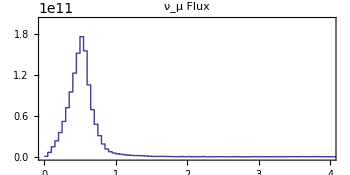

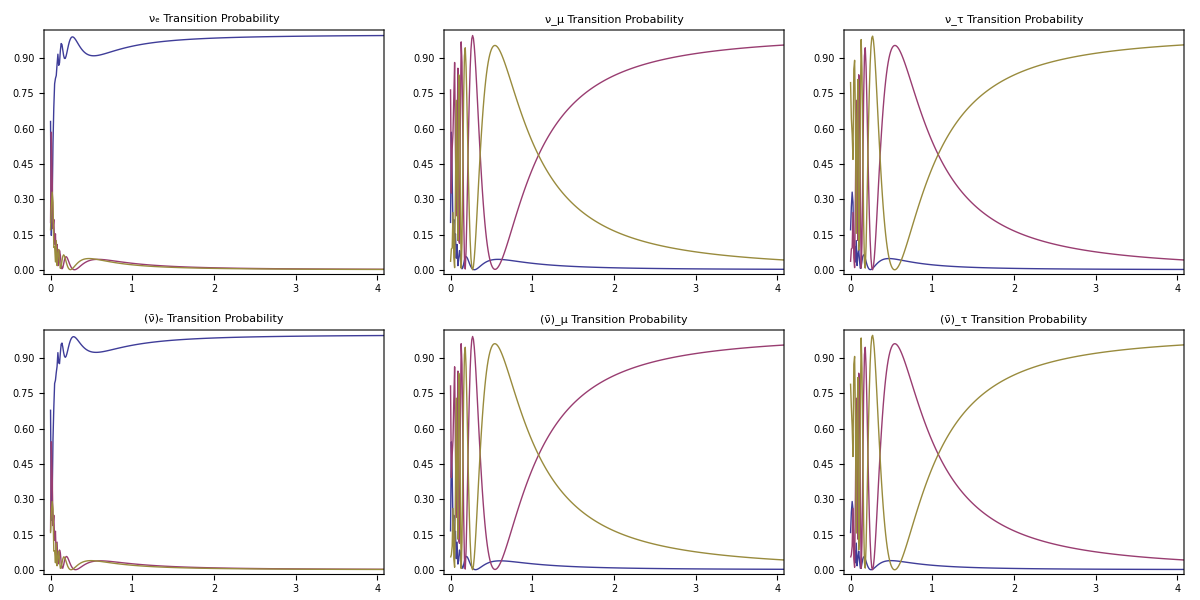

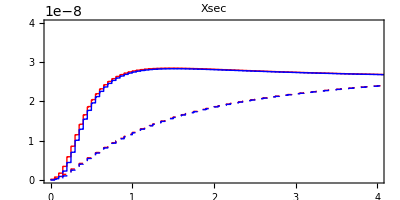

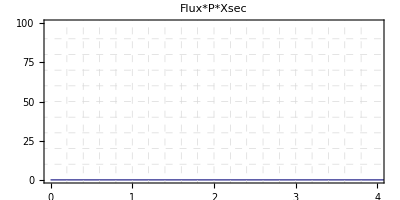

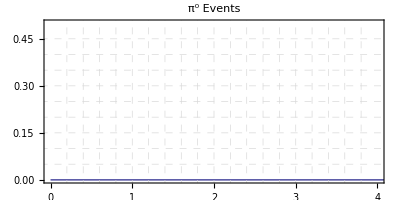

```mathematica
dir="rslt_xsecCC";
fluxNm=ReadList[FileNameJoin[{workdir,dir,"data","flux_nm.dat"}],Number,RecordLists->True];
probnene=ReadList[FileNameJoin[{workdir,dir,"data","prob_ne.ne.dat"}],Number,RecordLists->True];
probnenm=ReadList[FileNameJoin[{workdir,dir,"data","prob_ne.nm.dat"}],Number,RecordLists->True];
probnent=ReadList[FileNameJoin[{workdir,dir,"data","prob_ne.nt.dat"}],Number,RecordLists->True];
probnmne=ReadList[FileNameJoin[{workdir,dir,"data","prob_nm.ne.dat"}],Number,RecordLists->True];
probnmnm=ReadList[FileNameJoin[{workdir,dir,"data","prob_nm.nm.dat"}],Number,RecordLists->True];
probnmnt=ReadList[FileNameJoin[{workdir,dir,"data","prob_nm.nt.dat"}],Number,RecordLists->True];
probntne=ReadList[FileNameJoin[{workdir,dir,"data","prob_nt.ne.dat"}],Number,RecordLists->True];
probntnm=ReadList[FileNameJoin[{workdir,dir,"data","prob_nt.nm.dat"}],Number,RecordLists->True];
probntnt=ReadList[FileNameJoin[{workdir,dir,"data","prob_nt.nt.dat"}],Number,RecordLists->True];
probaeae=ReadList[FileNameJoin[{workdir,dir,"data","prob_ae.ae.dat"}],Number,RecordLists->True];
probaeam=ReadList[FileNameJoin[{workdir,dir,"data","prob_ae.am.dat"}],Number,RecordLists->True];
probaeat=ReadList[FileNameJoin[{workdir,dir,"data","prob_ae.at.dat"}],Number,RecordLists->True];
probamae=ReadList[FileNameJoin[{workdir,dir,"data","prob_am.ae.dat"}],Number,RecordLists->True];
probamam=ReadList[FileNameJoin[{workdir,dir,"data","prob_am.am.dat"}],Number,RecordLists->True];
probamat=ReadList[FileNameJoin[{workdir,dir,"data","prob_am.at.dat"}],Number,RecordLists->True];
probatae=ReadList[FileNameJoin[{workdir,dir,"data","prob_at.ae.dat"}],Number,RecordLists->True];
probatam=ReadList[FileNameJoin[{workdir,dir,"data","prob_at.am.dat"}],Number,RecordLists->True];
probatat=ReadList[FileNameJoin[{workdir,dir,"data","prob_at.at.dat"}],Number,RecordLists->True];
XsecCCne=ReadList[FileNameJoin[{workdir,dir,"data","xsec_cc_ne.dat"}],Number,RecordLists->True];
XsecCCnm=ReadList[FileNameJoin[{workdir,dir,"data","xsec_cc_nm.dat"}],Number,RecordLists->True];
XsecCCae=ReadList[FileNameJoin[{workdir,dir,"data","xsec_cc_ae.dat"}],Number,RecordLists->True];
XsecCCam=ReadList[FileNameJoin[{workdir,dir,"data","xsec_cc_am.dat"}],Number,RecordLists->True];
XsecNCne=ReadList[FileNameJoin[{workdir,dir,"data","xsec_nc_ne.dat"}],Number,RecordLists->True];
XsecNCnm=ReadList[FileNameJoin[{workdir,dir,"data","xsec_nc_nm.dat"}],Number,RecordLists->True];
XsecNCae=ReadList[FileNameJoin[{workdir,dir,"data","xsec_nc_ae.dat"}],Number,RecordLists->True];
XsecNCam=ReadList[FileNameJoin[{workdir,dir,"data","xsec_nc_am.dat"}],Number,RecordLists->True];
FluxPXsec=ReadList[FileNameJoin[{workdir,dir,"data","flux_P_xsec.dat"}],Number,RecordLists->True];
Pi0Event=ReadList[FileNameJoin[{workdir,dir,"data","pi0event.dat"}],Number,RecordLists->True];

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=4;
ymin=0;ymax=2 10^11;
xdiv=0.2;
ydiv=ymax/10;
title="ν_μ Flux";
options={AspectRatio->0.5,ImageSize->350};
(*flux=ListLogPlotHG[{flux},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]*)
flux=ListPlotHG[fluxNm,title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]

ymin=0;ymax=1;
ydiv=ymax/10;
options={AspectRatio->0.5,ImageSize->300,Joined->True};
title="ν_e Transition Probability";
ProbNe=ListPlotG[{probnene,probnenm,probnent},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];
title="ν_μ Transition Probability";
ProbNm=ListPlotG[{probnmne,probnmnm,probnmnt},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];
title="ν_τ Transition Probability";
ProbNt=ListPlotG[{probntne,probntnm,probntnt},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];
title="(ν̄)_e Transition Probability";
ProbAe=ListPlotG[{probaeae,probaeam,probaeat},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];
title="(ν̄)_μ Transition Probability";
ProbAm=ListPlotG[{probamae,probamam,probamat},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];
title="(ν̄)_τ Transition Probability";
ProbAt=ListPlotG[{probatae,probatam,probatat},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];
Grid@Partition[{ProbNe,ProbNm,ProbNt,ProbAe,ProbAm,ProbAt},3]

ymin=0;ymax=4 10^-8;
ydiv=ymax/10;
title="Xsec";
options={AspectRatio->0.5,ImageSize->400,PlotStyle->{Red,Blue,{Red,Dashed},{Blue,Dashed}}};
xsecCC=ListPlotHG[{XsecCCne,XsecCCnm,XsecCCae,XsecCCam},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];
xsecNC=ListPlotHG[{XsecNCne,XsecNCnm,XsecNCae,XsecNCam},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];
Show[{xsecCC}]

ymin=0;ymax=100;
ydiv=ymax/10;
title="Flux*P*Xsec";
options={AspectRatio->0.5,ImageSize->400(*,PlotStyle->Blue*)};
xsecCC=ListPlotHG[FluxPXsec,title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]

ymin=0;ymax=0.5;
ydiv=ymax/10;
title="π^0 Events";
options={AspectRatio->0.5,ImageSize->400(*,PlotStyle->Blue*)};
xsecCC=ListPlotHG[Pi0Event,title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

```mathematica
100/960.
```

0.104167

```mathematica
13000000(0.104167-0.097860)
```

81991.

```mathematica
130000000
```

## NCpi0 component plot

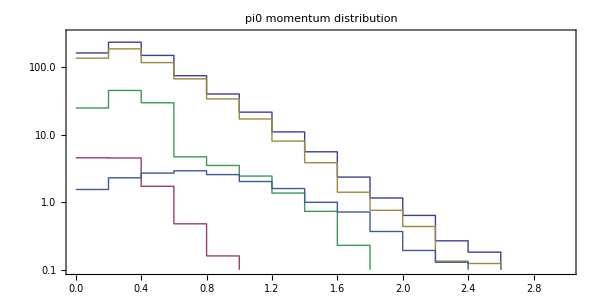

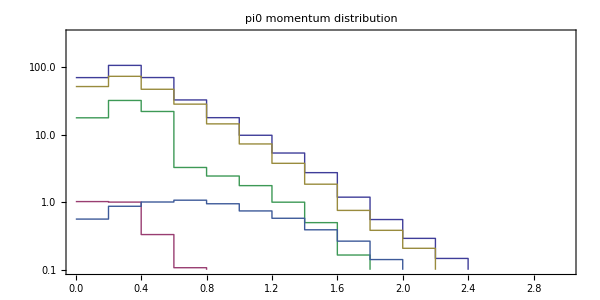

```mathematica
ncqe=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_Erec_ncqe","data","event_pi0bg.dat"}],Number,RecordLists->True];
ncrs=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_Erec_ncrs","data","event_pi0bg.dat"}],Number,RecordLists->True];
ncco=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_Erec_ncco","data","event_pi0bg.dat"}],Number,RecordLists->True];
ncdi=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_Erec_ncdi","data","event_pi0bg.dat"}],Number,RecordLists->True];

total=Table[{ncqe[[i,1]],ncrs[[i,2]]+ncco[[i,2]]+ncdi[[i,2]]},{i,1,Length[ncqe]}];

Export["ncqe.inv_200.dat",ncqe,"Table"];
Export["ncrs.inv_200.dat",ncrs,"Table"];
Export["ncco.inv_200.dat",ncco,"Table"];
Export["ncdi.inv_200.dat",ncdi,"Table"];
Export["total.inv_200.dat",total,"Table"];

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=3;
ymin=0.1;ymax=300;
xdiv=xmax/15;
ydiv=ymax/10;
title="pi0 momentum distribution";
options={AspectRatio->0.5,ImageSize->600(*,PlotStyle->Blue*)};
ListLogPlotHG[{total,ncqe,ncrs,ncco,ncdi},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]


ncqea=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_Erec_ncqe.a","data","event_pi0bg.dat"}],Number,RecordLists->True];
ncrsa=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_Erec_ncrs.a","data","event_pi0bg.dat"}],Number,RecordLists->True];
nccoa=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_Erec_ncco.a","data","event_pi0bg.dat"}],Number,RecordLists->True];
ncdia=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_Erec_ncdi.a","data","event_pi0bg.dat"}],Number,RecordLists->True];

totala=Table[{ncqea[[i,1]],ncrsa[[i,2]]+nccoa[[i,2]]+ncdia[[i,2]]},{i,1,Length[ncqe]}];

Export["ncqe.inv.a_200.dat",ncqea,"Table"];
Export["ncrs.inv.a_200.dat",ncrsa,"Table"];
Export["ncco.inv.a_200.dat",nccoa,"Table"];
Export["ncdi.inv.a_200.dat",ncdia,"Table"];
Export["total.inv.a_200.dat",totala,"Table"];

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=3;
ymin=0.1;ymax=300;
xdiv=xmax/15;
ydiv=ymax/10;
title="pi0 momentum distribution";
options={AspectRatio->0.5,ImageSize->600(*,PlotStyle->Blue*)};
ListLogPlotHG[{totala,ncqea,ncrsa,nccoa,ncdia},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

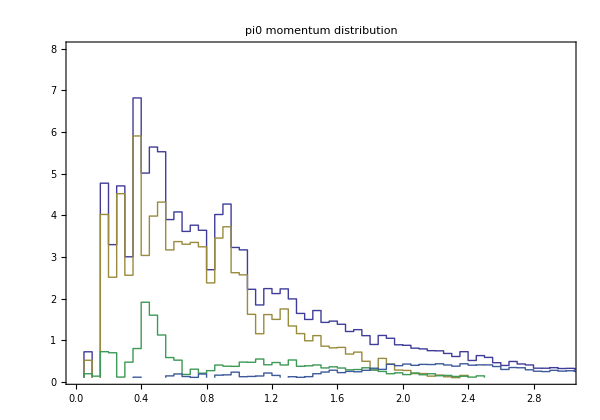

```mathematica
ncqe=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncqe_50.dat"}],Number,RecordLists->True];
ncrs=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncrs_50.dat"}],Number,RecordLists->True];
ncco=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncco_50.dat"}],Number,RecordLists->True];
ncdi=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncdi_50.dat"}],Number,RecordLists->True];
total=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","total_50.dat"}],Number,RecordLists->True];
ncqeinv=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncqe.inv_50.dat"}],Number,RecordLists->True];
ncrsinv=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncrs.inv_50.dat"}],Number,RecordLists->True];
nccoinv=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncco.inv_50.dat"}],Number,RecordLists->True];
ncdiinv=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncdi.inv_50.dat"}],Number,RecordLists->True];
totalinv=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","total.inv_50.dat"}],Number,RecordLists->True];

ncqepol=Table[{ncqe[[i,1]],ncqe[[i,2]]-ncqeinv[[i,2]]},{i,1,Length[ncqe]}];
ncrspol=Table[{ncrs[[i,1]],ncrs[[i,2]]-ncrsinv[[i,2]]},{i,1,Length[ncrs]}];
nccopol=Table[{ncco[[i,1]],ncco[[i,2]]-nccoinv[[i,2]]},{i,1,Length[ncco]}];
ncdipol=Table[{ncdi[[i,1]],ncdi[[i,2]]-ncdiinv[[i,2]]},{i,1,Length[ncdi]}];
totalpol=Table[{total[[i,1]],total[[i,2]]-totalinv[[i,2]]},{i,1,Length[total]}];

Export["ncqe.inv.a_200.dat",ncqepol,"Table"];
Export["ncrs.inv.a_200.dat",ncrspol,"Table"];
Export["ncco.inv.a_200.dat",nccopol,"Table"];
Export["ncdi.inv.a_200.dat",ncdipol,"Table"];
Export["total.inv.a_200.dat",totalpol,"Table"];

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=3;
ymin=0.1;ymax=8;
xdiv=xmax/15;
ydiv=ymax/10;
title="pi0 momentum distribution";
options={AspectRatio->0.7,ImageSize->600(*,PlotStyle->Blue*)};
ListPlotHG[{totalpol,ncqepol,ncrspol,nccopol,ncdipol},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

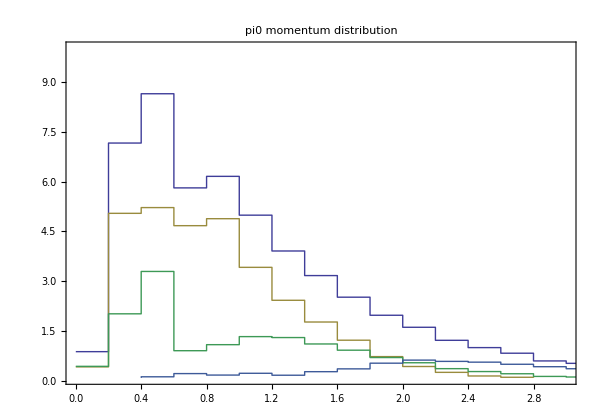

```mathematica
ncqe=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncqe.a_200.dat"}],Number,RecordLists->True];
ncrs=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncrs.a_200.dat"}],Number,RecordLists->True];
ncco=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncco.a_200.dat"}],Number,RecordLists->True];
ncdi=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncdi.a_200.dat"}],Number,RecordLists->True];
total=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","total.a_200.dat"}],Number,RecordLists->True];
ncqeinv=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncqe.inv.a_200.dat"}],Number,RecordLists->True];
ncrsinv=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncrs.inv.a_200.dat"}],Number,RecordLists->True];
nccoinv=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncco.inv.a_200.dat"}],Number,RecordLists->True];
ncdiinv=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","ncdi.inv.a_200.dat"}],Number,RecordLists->True];
totalinv=ReadList[FileNameJoin[{workdir,"figures","pi0_Erec_proc","total.inv.a_200.dat"}],Number,RecordLists->True];

ncqepol=Table[{ncqe[[i,1]],ncqe[[i,2]]-ncqeinv[[i,2]]},{i,1,Length[ncqe]}];
ncrspol=Table[{ncrs[[i,1]],ncrs[[i,2]]-ncrsinv[[i,2]]},{i,1,Length[ncrs]}];
nccopol=Table[{ncco[[i,1]],ncco[[i,2]]-nccoinv[[i,2]]},{i,1,Length[ncco]}];
ncdipol=Table[{ncdi[[i,1]],ncdi[[i,2]]-ncdiinv[[i,2]]},{i,1,Length[ncdi]}];
totalpol=Table[{total[[i,1]],total[[i,2]]-totalinv[[i,2]]},{i,1,Length[total]}];

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=3;
ymin=0.1;ymax=10;
xdiv=xmax/15;
ydiv=ymax/10;
title="pi0 momentum distribution";
options={AspectRatio->0.7,ImageSize->600(*,PlotStyle->Blue*)};
ListPlotHG[{totalpol,ncqepol,ncrspol,nccopol,ncdipol},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

## missID plot

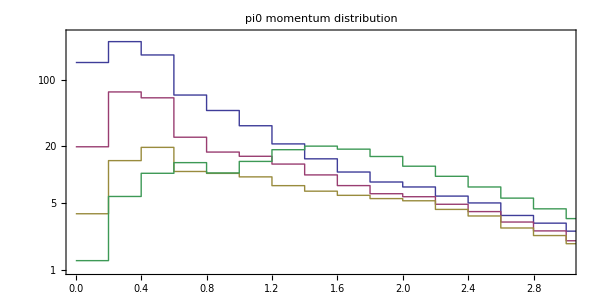

```mathematica
noveto=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_noveto","data","event_pi0bg.dat"}],Number,RecordLists->True];
oldveto=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_oldveto","data","event_pi0bg.dat"}],Number,RecordLists->True];
polfit=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_polfit","data","event_pi0bg.dat"}],Number,RecordLists->True];
nmnee=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_polfit","data","event_nm.ne.e.dat"}],Number,RecordLists->True];
nenee=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_polfit","data","event_ne.ne.e.dat"}],Number,RecordLists->True];
amaee=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_polfit","data","event_am.ae.e.dat"}],Number,RecordLists->True];
aeaee=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_polfit","data","event_ae.ae.e.dat"}],Number,RecordLists->True];

signal=Table[{nmnee[[i,1]],nmnee[[i,2]]+nenee[[i,2]]+amaee[[i,2]]+aeaee[[i,2]]},{i,1,Length[nmnee]}];
noveto2={#[[1]],2#[[2]]}&/@noveto;
oldveto2={#[[1]],2#[[2]]}&/@oldveto;
polfit2={#[[1]],2#[[2]]}&/@polfit;

Export["noveto.dat",noveto,"Table"];
Export["oldveto.dat",oldveto,"Table"];
Export["polfit.dat",polfit,"Table"];
Export["signal.dat",signal,"Table"];

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=3;
ymin=1;ymax=300;
xdiv=xmax/15;
ydiv=ymax/10;
title="pi0 momentum distribution";
options={AspectRatio->0.5,ImageSize->600(*,PlotStyle->Blue*)};
ListLogPlotHG[{noveto,oldveto,polfit,signal},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

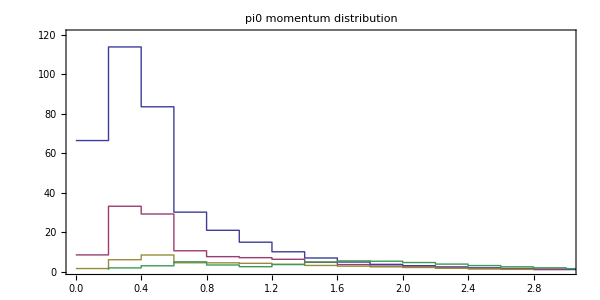

```mathematica
noveto=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_noveto.a","data","event_pi0bg.dat"}],Number,RecordLists->True];
oldveto=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_oldveto.a","data","event_pi0bg.dat"}],Number,RecordLists->True];
polfit=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_polfit.a","data","event_pi0bg.dat"}],Number,RecordLists->True];
nmnee=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_polfit.a","data","event_nm.ne.e.dat"}],Number,RecordLists->True];
nenee=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_polfit.a","data","event_ne.ne.e.dat"}],Number,RecordLists->True];
amaee=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_polfit.a","data","event_am.ae.e.dat"}],Number,RecordLists->True];
aeaee=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_polfit.a","data","event_ae.ae.e.dat"}],Number,RecordLists->True];

signal=Table[{nmnee[[i,1]],nmnee[[i,2]]+nenee[[i,2]]+amaee[[i,2]]+aeaee[[i,2]]},{i,1,Length[nmnee]}];
noveto2={#[[1]],2#[[2]]}&/@noveto;
oldveto2={#[[1]],2#[[2]]}&/@oldveto;
polfit2={#[[1]],2#[[2]]}&/@polfit;

Export["noveto.a.dat",noveto,"Table"];
Export["oldveto.a.dat",oldveto,"Table"];
Export["polfit.a.dat",polfit,"Table"];
Export["signal.a.dat",signal,"Table"];

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=3;
ymin=1;ymax=120;
xdiv=xmax/15;
ydiv=ymax/10;
title="pi0 momentum distribution";
options={AspectRatio->0.5,ImageSize->600(*,PlotStyle->Blue*)};
ListPlotHG[{noveto,oldveto,polfit,signal},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

## Convolution test

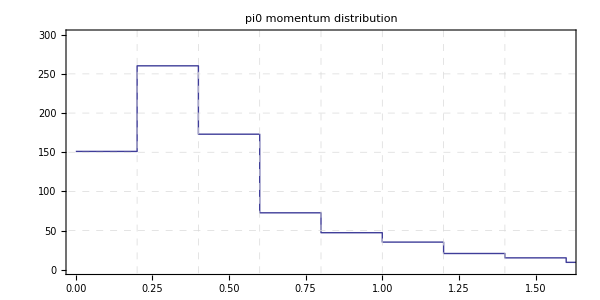

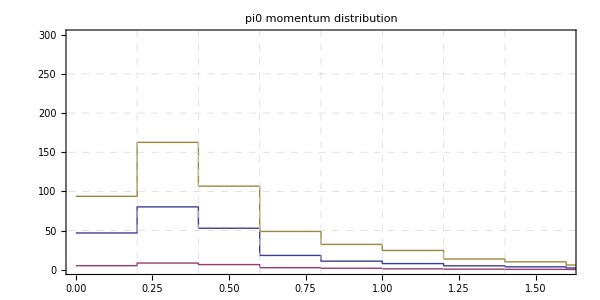

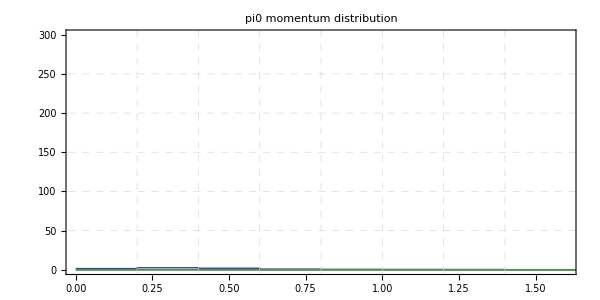

```mathematica
pi0bg=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_pi0bg.dat"}],Number,RecordLists->True];
pi0bgnmnm=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_nm.nm.pi0.dat"}],Number,RecordLists->True];
pi0bgnmne=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_nm.ne.pi0.dat"}],Number,RecordLists->True];
pi0bgnmnt=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_nm.nt.pi0.dat"}],Number,RecordLists->True];
pi0bgnenm=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_ne.nm.pi0.dat"}],Number,RecordLists->True];
pi0bgnene=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_ne.ne.pi0.dat"}],Number,RecordLists->True];
pi0bgnent=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_ne.nt.pi0.dat"}],Number,RecordLists->True];
pi0bgamam=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_am.am.pi0.dat"}],Number,RecordLists->True];
pi0bgamae=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_am.ae.pi0.dat"}],Number,RecordLists->True];
pi0bgamat=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_am.at.pi0.dat"}],Number,RecordLists->True];
pi0bgaeam=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_ae.am.pi0.dat"}],Number,RecordLists->True];
pi0bgaeae=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_ae.ae.pi0.dat"}],Number,RecordLists->True];
pi0bgaeat=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_ae.at.pi0.dat"}],Number,RecordLists->True];
(*data3=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_signal.dat"}],Number,RecordLists->True];
datanc=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_nc.dat"}],Number,RecordLists->True];
datapi0bg=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event_pi0bg.dat"}],Number,RecordLists->True];
data4=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","event.dat"}],Number,RecordLists->True];*)
col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=1.6;
ymin=0;ymax=300;
xdiv=xmax/8;
ydiv=ymax/6;
title="pi0 momentum distribution";
options={AspectRatio->0.5,ImageSize->600(*,PlotStyle->Blue*)};
ListPlotHG[{pi0bg},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
ListPlotHG[{pi0bgnmnm,pi0bgnmne,pi0bgnmnt},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
ListPlotHG[{pi0bgamam,pi0bgamae,pi0bgaeam,pi0bgaeae},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

## Sensitivity

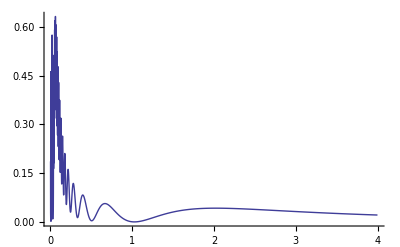

```mathematica
data=ReadList[FileNameJoin[{workdir,"beam_neu_minimize/rslt_test/data/event.dat"}],Number,RecordLists->True];
data2={#[[1]],#[[2]]}&/@data;
ListPlot[data2,Joined->True]
```

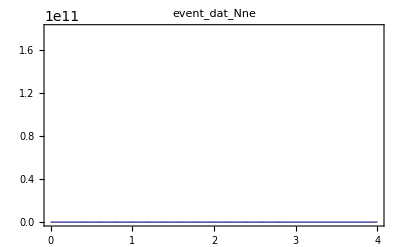

```mathematica
col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=4;
ymin=0;ymax=18 10^10;
xdiv=0.2;
ydiv=2 10^10;
title="event_dat_Nne";
path=FileNameJoin[{workdir,"beam_neu_minimize/","rslt_test","data","event.dat"}];
ListPlotHG[title,path,col1,col2,PP,AP,xmin,xmax,ymin,ymax,xdiv,ydiv]
```

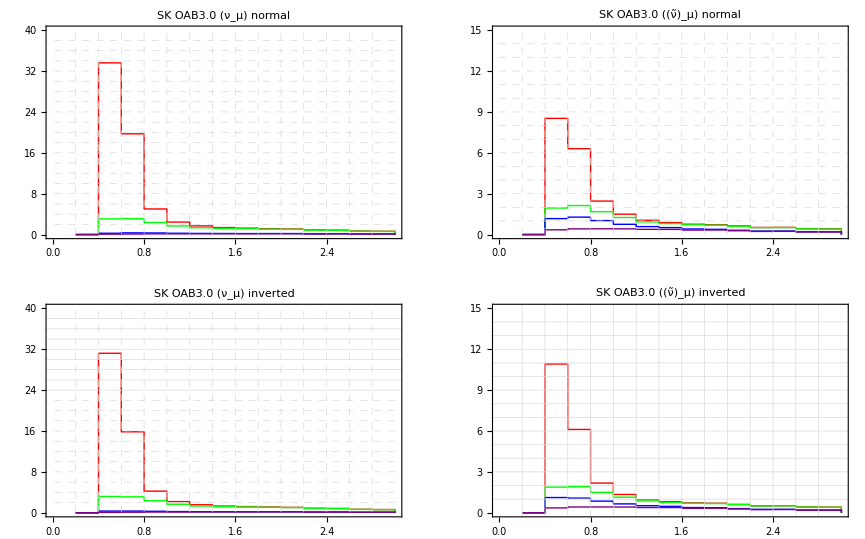

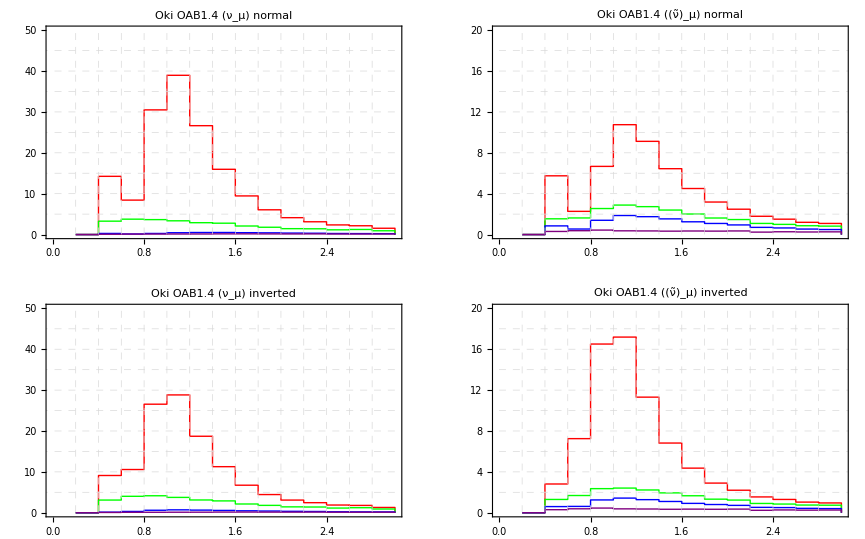

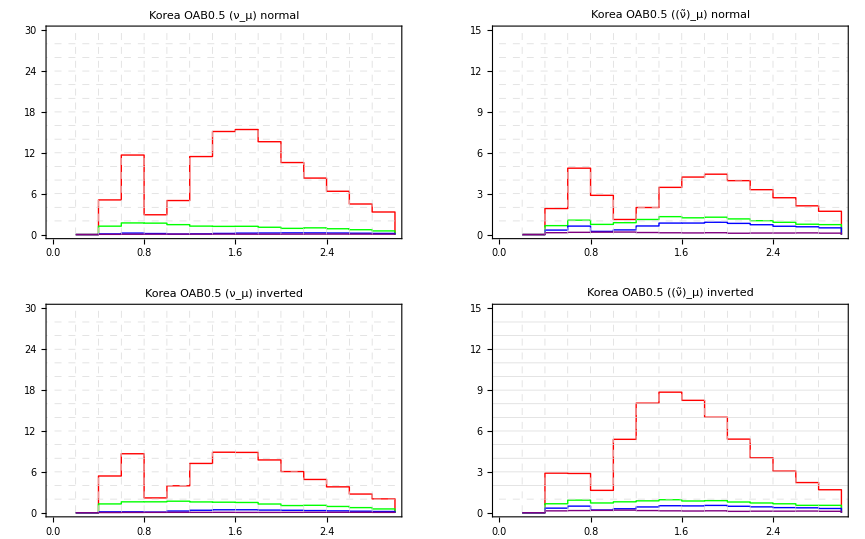

```mathematica
GraphicsGrid[{{EventNumPlot["SK OAB3.0 (ν_μ) normal","sknn_mue","sknn_ee","sknn_muaea","sknn_eaea",3,40,0.2,2],
EventNumPlot["SK OAB3.0 ((ν̃)_μ) normal","skna_muaea","skna_eaea","skna_mue","skna_ee",3,15,0.2,1]},{
EventNumPlot["SK OAB3.0 (ν_μ) inverted","skin_mue","skin_ee","skin_muaea","skin_eaea",3,40,0.2,2],
EventNumPlot["SK OAB3.0 ((ν̃)_μ) inverted","skia_muaea","skia_eaea","skia_mue","skia_ee",3,15,0.2,1]}}]
GraphicsGrid[{{EventNumPlot["Oki OAB1.4 (ν_μ) normal","Oknn_mue","Oknn_ee","Oknn_muaea","Oknn_eaea",3,50,0.2,5],
EventNumPlot["Oki OAB1.4 ((ν̃)_μ) normal","okna_muaea","okna_eaea","okna_mue","okna_ee",3,20,0.2,2]},{
EventNumPlot["Oki OAB1.4 (ν_μ) inverted","okin_mue","okin_ee","okin_muaea","okin_eaea",3,50,0.2,5],
EventNumPlot["Oki OAB1.4 ((ν̃)_μ) inverted","okia_muaea","okia_eaea","okia_mue","okia_ee",3,20,0.2,2]}}]
GraphicsGrid[{{EventNumPlot["Korea OAB0.5 (ν_μ) normal","krnn_mue","krnn_ee","krnn_muaea","krnn_eaea",3,30,0.2,2],
EventNumPlot["Korea OAB0.5 ((ν̃)_μ) normal","krna_muaea","krna_eaea","krna_mue","krna_ee",3,15,0.2,1]},{
EventNumPlot["Korea OAB0.5 (ν_μ) inverted","krin_mue","krin_ee","krin_muaea","krin_eaea",3,30,0.2,2],
EventNumPlot["Korea OAB0.5 ((ν̃)_μ) inverted","kria_muaea","kria_eaea","kria_mue","kria_ee",3,15,0.2,1]}}]
```

```mathematica
maindir="beam_neu_minimize/";
rundir="prjct_dchi22.10_2";
data=ReadList[FileNameJoin[{workdir,maindir,rundir,"dchi2_kr.dat"}],Number,RecordLists->True];
datanh={#[[1]],#[[2]],#[[4]],#[[6]]}&/@data;
datanh=PrependTo[datanh,{0,2,2.5,3}];
datanh=Drop[Transpose[datanh],1];
krnh0={#[[1]],#[[2]]}&/@datanh;
krnh90={#[[1]],#[[3]]}&/@datanh;
krnh180={#[[1]],#[[4]]}&/@datanh;
krnh270={#[[1]],#[[5]]}&/@datanh;
dataih={#[[1]],#[[3]],#[[5]],#[[7]]}&/@data;
dataih=PrependTo[dataih,{0,2,2.5,3}];
dataih=Drop[Transpose[dataih],1];
krih0={#[[1]],#[[2]]}&/@dataih;
krih90={#[[1]],#[[3]]}&/@dataih;
krih180={#[[1]],#[[4]]}&/@dataih;
krih270={#[[1]],#[[5]]}&/@dataih;
data=ReadList[FileNameJoin[{workdir,maindir,rundir,"dchi2_ok.dat"}],Number,RecordLists->True];
datanh={#[[1]],#[[2]],#[[4]],#[[6]]}&/@data;
datanh=PrependTo[datanh,{0,2,2.5,3}];
datanh=Drop[Transpose[datanh],1];
oknh0={#[[1]],#[[2]]}&/@datanh;
oknh90={#[[1]],#[[3]]}&/@datanh;
oknh180={#[[1]],#[[4]]}&/@datanh;
oknh270={#[[1]],#[[5]]}&/@datanh;
dataih={#[[1]],#[[3]],#[[5]],#[[7]]}&/@data;
dataih=PrependTo[dataih,{0,2,2.5,3}];
dataih=Drop[Transpose[dataih],1];
okih0={#[[1]],#[[2]]}&/@dataih;
okih90={#[[1]],#[[3]]}&/@dataih;
okih180={#[[1]],#[[4]]}&/@dataih;
okih270={#[[1]],#[[5]]}&/@dataih;
data=ReadList[FileNameJoin[{workdir,maindir,rundir,"dchi2_sk.dat"}],Number,RecordLists->True];
datanh={#[[1]],#[[2]],#[[4]],#[[6]]}&/@data;
datanh=PrependTo[datanh,{0,2,2.5,3}];
datanh=Drop[Transpose[datanh],1];
sknh0={#[[1]],#[[2]]}&/@datanh;
sknh90={#[[1]],#[[3]]}&/@datanh;
sknh180={#[[1]],#[[4]]}&/@datanh;
sknh270={#[[1]],#[[5]]}&/@datanh;
dataih={#[[1]],#[[3]],#[[5]],#[[7]]}&/@data;
dataih=PrependTo[dataih,{0,2,2.5,3}];
dataih=Drop[Transpose[dataih],1];
skih0={#[[1]],#[[2]]}&/@dataih;
skih90={#[[1]],#[[3]]}&/@dataih;
skih180={#[[1]],#[[4]]}&/@dataih;
skih270={#[[1]],#[[5]]}&/@dataih;
```

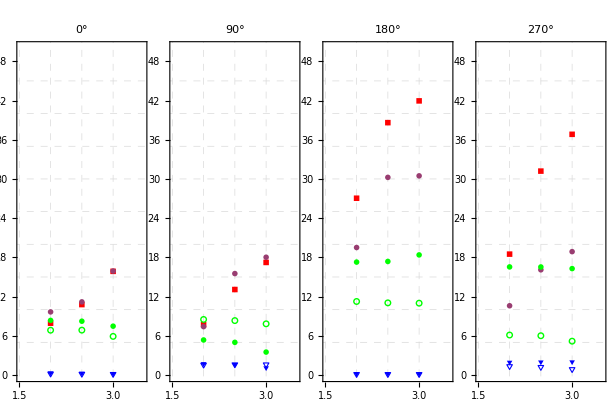

```mathematica
col1=1;col2=2;
PP=0;AP=4;
xmin=1.5;xmax=3.5;
ymin=0;ymax=50;
xdiv=0.5;
ydiv=5;
title0="0°";title90="90°";title180="180°";title270="270°";
{so,sc}=Graphics[{Red,#}]&/@{Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}]};
{co,cc}=Graphics[{Green,#}]&/@{Circle[{0,0},1],Disk[{0,0},1]};
to=Graphics[{White,EdgeForm[Directive[Thick,Blue]],Polygon[{{0,Sqrt[3]/2},{0.5,0},{1,Sqrt[3]/2}}]}];
tc=Graphics[{Blue,Polygon[{{0,Sqrt[3]/2},{0.5,0},{1,Sqrt[3]/2}}]}];
options={PlotMarkers->Table[{s,0.1},{s,{sc,so,cc,co,to,tc}}],AspectRatio->2.7,ImageSize->150};
GraphicsGrid[{{ListPlotG[{krnh0,krih0,oknh0,okih0,skih0,sknh0},title0,xmin,xmax,ymin,ymax,xdiv,ydiv,options],ListPlotG[{krnh90,krih90,oknh90,okih90,skih90,sknh90},title90,xmin,xmax,ymin,ymax,xdiv,ydiv,options],
ListPlotG[{krnh180,krih180,oknh180,okih180,skih180,sknh180},title180,xmin,xmax,ymin,ymax,xdiv,ydiv,options],ListPlotG[{krnh270,krih270,oknh270,okih270,skih270,sknh270},title270,xmin,xmax,ymin,ymax,xdiv,ydiv,options]}},Spacings->{0,0}]
```

```mathematica
a
```

-Graphics-

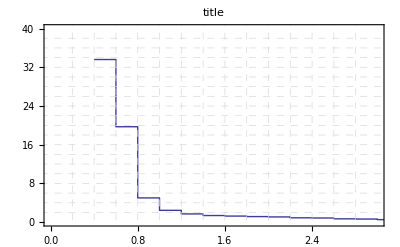

```mathematica
data=ReadList[FileNameJoin[{workdir,"beam_neu_minimize/","rslt_test","data","event.dat"}],Number,RecordLists->True];
col1=1;col2=2;
PP=0.2;AP=3;
xmin=0;xmax=3;
ymin=0;ymax=40;
xdiv=0.2;
ydiv=2;
title="title";
options={};
ListPlotHG[data,title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

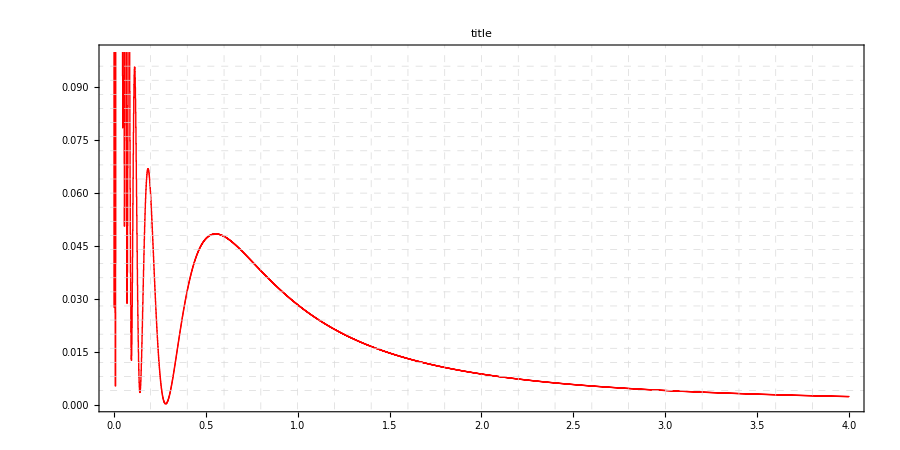

```mathematica
data=ReadList[FileNameJoin[{workdir,"beam_neu_minimize/","rslt_test","data","event.dat"}],Number,RecordLists->True];
col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=4;
ymin=0;ymax=0.1;
xdiv=0.2;
ydiv=0.004;
title="title";
options={AspectRatio->0.5,ImageSize->900,PlotStyle->Red};
num=ListPlotHG[data,title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

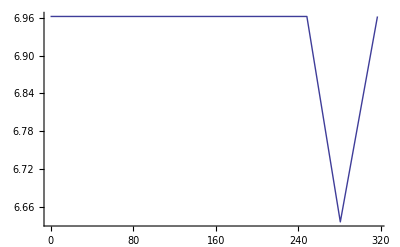

```mathematica
data=ReadList[FileNameJoin[{workdir,"beam_neu_minimize_parallel/","prjct_test","rslt_ok_1_2.5_5_-1_0","dchi2_scan_ok_1_2.5_5_-1_0.dat"}],Number,RecordLists->True];
ListPlot[data,Joined->True,PlotRange->All]
```

```mathematica
{{0.4,130.838035},{0.600000003,242.88277},{0.800000006,159.190106},{1.00000001,59.7242796}}
```

```mathematica
38 4
```

152

```mathematica
180/360. *2Pi
```

4.71239

```mathematica
2.Pi
```

6.28319

```mathematica
134/360. 2 Pi
```

2.33874

```mathematica
61.4354424-67.0611452
```

-5.6257

```mathematica
53.5632106-59.1889134
```

-5.6257

```mathematica
67.2058748-67.0611452
```

0.14473

```mathematica
59.333643-59.1889134
```

0.14473

```mathematica
61.4354424-61.0723269
```

0.363115

```mathematica
53.5632106-53.2000951
```

0.363115

```mathematica
61.0723269-53.2000951
```

7.87223

```mathematica
s2sol2=0.852;
satm2=0.5;
s2rct2=0.08;
satm=√satm2;
srct2=(1-√(1-s2rct2))/2;
s132=srct2;
s2sol=√s2sol2;
s212=s2sol/(1-s132);
s2122=s212^2
s23=satm/√(1-s132);
s2232=4 s23^2 (1-s23^2)
```

0.887886

0.999566

```mathematica
s2atm2=1.;
s2rct2=0.08;
satm2=(1-√(1-s2atm2))/2
satm=√satm2;
s2132=s2rct2;
s132=(1-√(1-s2132))/2;
s23=satm/√(1-s132)
s2232=4 s23^2 (1-s23^2)
```

0.5

0.714438

0.999566

```mathematica
$Assumptions=1>as2rct2>0&&1>as2atm2>0;
srct2=(1-√(1-as2rct2))/2;
srct=√srct2;
s13=srct;
satm2=(1+√(1-as2atm2))/2;
satm=√satm2;
s23=satm/√(1-s13^2);
s2232=4 s23^2 (1-s23^2);
s2132=as2rct2;
bs232=(1-√(1-s2232))/2;
bs23=√bs232;
bs132=(1-√(1-s2132))/2;
bsatm=bs23 √(1-bs132);
bs2atm2=4 bsatm^2(1-bsatm^2)//FullSimplify
```

-1-√(1-as2atm2)+as2atm2+√(1-as2rct2)+√((-1+as2atm2) (-1+as2rct2))+1/2 (as2rct2-as2rct2 √(-(-6-4 √(1-as2atm2)+4 as2atm2+2 √(1-as2rct2)+4 √((-1+as2atm2) (-1+as2rct2))+as2rct2)/(1+√(1-as2rct2))^2))

```mathematica
bs2atm2/.{as2atm2->1,as2rct2->0.08}
```

0.998333

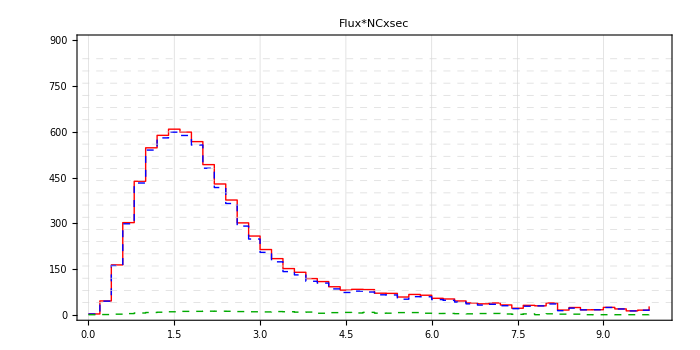

```mathematica
datanm=ReadList[FileNameJoin[{workdir,"beam_neu_run/","rslt_testnm","data","event.dat"}],Number,RecordLists->True];
dataam=ReadList[FileNameJoin[{workdir,"beam_neu_run/","rslt_testam","data","event.dat"}],Number,RecordLists->True];
datanm1=#[[1]]&/@datanm;
datanm2=#[[2]]&/@datanm;
dataam2=#[[2]]&/@dataam;
datasum=datanm2+dataam2;
data=Table[{datanm1[[i]],datasum[[i]]},{i,1,Length[datanm]}];
col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=10;
ymin=0;ymax=9 10^2;
xdiv=0.2;
ydiv=40;
title="Flux*NCxsec";
options={AspectRatio->0.5,ImageSize->700,PlotStyle->{Red,{Blue,Dashed},{Darker[Green],Dashed}}};
num=ListPlotHG[{data,datanm,dataam},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

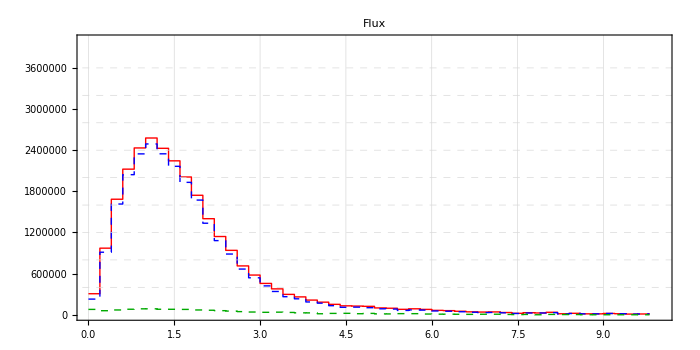

```mathematica
datanm=ReadList[FileNameJoin[{workdir,"beam_neu_run/","rslt_fluxnm","data","event.dat"}],Number,RecordLists->True];
dataam=ReadList[FileNameJoin[{workdir,"beam_neu_run/","rslt_fluxam","data","event.dat"}],Number,RecordLists->True];
datanm1=#[[1]]&/@datanm;
datanm2=#[[2]]&/@datanm;
dataam2=#[[2]]&/@dataam;
datasum=datanm2+dataam2;
data=Table[{datanm1[[i]],datasum[[i]]},{i,1,Length[datanm]}];
col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=10;
ymin=0;ymax=4 10^6;
xdiv=0.2;
ydiv=4 10^5;
title="Flux";
options={AspectRatio->0.5,ImageSize->700,PlotStyle->{Red,{Blue,Dashed},{Darker[Green],Dashed}}};
num=ListPlotHG[{data,datanm,dataam},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

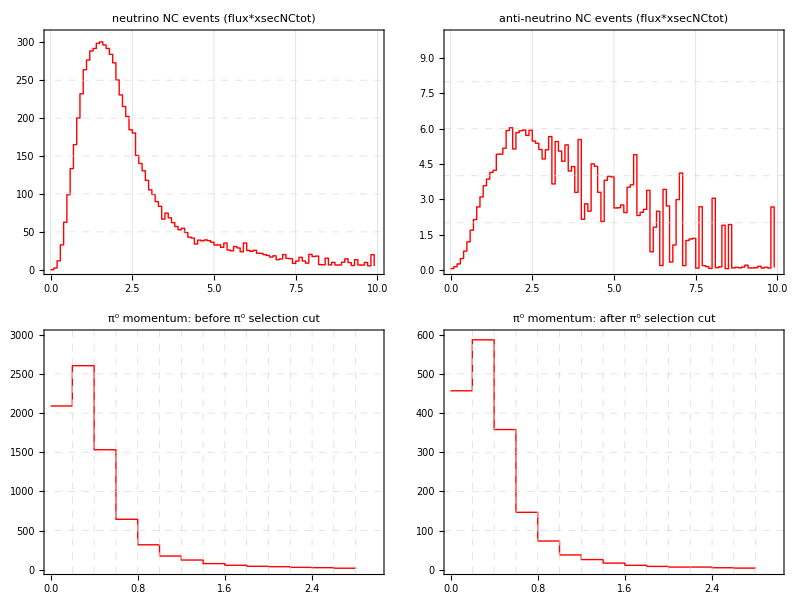

```mathematica
rationm=ReadList[FileNameJoin[{workdir,"beam_neu_run/","rslt_testnm","data","ratio2.dat"}],Number,RecordLists->True];
ratioanm=ReadList[FileNameJoin[{workdir,"beam_neu_run/","rslt_testanm","data","ratio2.dat"}],Number,RecordLists->True];
rationm=rationm//Flatten;
ratioanm=ratioanm//Flatten;
rationmlist=ReadList[FileNameJoin[{workdir,"beam_neu_run/","rslt_testnm","data","event.dat"}],Number,RecordLists->True];
ratioanmlist=ReadList[FileNameJoin[{workdir,"beam_neu_run/","rslt_testanm","data","event.dat"}],Number,RecordLists->True];

y=Table[0,{i,1,15}];
Do[
filenm="nm"<>ToString[50+100(j-1)]<>"_ma1100.dat";
fileanm="anm"<>ToString[50+100(j-1)]<>"_ma1100.dat";
histnm=ReadList[FileNameJoin[{workdir,"nuance_work/pi0/","pi0dist_cut",filenm}],Number,RecordLists->True];
histanm=ReadList[FileNameJoin[{workdir,"nuance_work/pi0/","pi0dist_cut",fileanm}],Number,RecordLists->True];
x=(#[[1]]-100)&/@histnm;
ynm=#[[2]]&/@histnm;
yanm=#[[2]]&/@histanm;
y=y+ynm rationm[[j]]/1000.+yanm ratioanm[[j]]/1000.;
,{j,1,100}]
histcut=Table[{x[[i]]/1000.,y[[i]]},{i,1,15}];

y=Table[0,{i,1,15}];
Do[
filenm="nm"<>ToString[50+100(j-1)]<>"_ma1100.dat";
fileanm="anm"<>ToString[50+100(j-1)]<>"_ma1100.dat";
histnm=ReadList[FileNameJoin[{workdir,"nuance_work/pi0/","pi0dist",filenm}],Number,RecordLists->True];
histanm=ReadList[FileNameJoin[{workdir,"nuance_work/pi0/","pi0dist",fileanm}],Number,RecordLists->True];
x=(#[[1]]-100)&/@histnm;
ynm=#[[2]]&/@histnm;
yanm=#[[2]]&/@histanm;
y=y+ynm rationm[[j]]/1000.+yanm ratioanm[[j]]/1000.;
,{j,1,100}]
hist=Table[{x[[i]]/1000.,y[[i]]},{i,1,15}];

PlotSize=400;
col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=10;
ymin=0;ymax=310;
xdiv=0.2;
ydiv=5 10;
title="neutrino NC events (flux*xsecNCtot)";
options={AspectRatio->0.5,ImageSize->PlotSize,PlotStyle->Red};
a1=ListPlotHG[{rationmlist},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];

ymin=0;ymax=10;
ydiv=2 ;
title="anti-neutrino NC events (flux*xsecNCtot)";
options={AspectRatio->0.5,ImageSize->PlotSize,PlotStyle->Red};
a2=ListPlotHG[{ratioanmlist},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=3;
ymin=0;ymax=3000;
xdiv=0.2;
ydiv=5 10^2;
title="π^0 momentum: before π^0 selection cut";
options={AspectRatio->0.5,ImageSize->PlotSize,PlotStyle->Red};
b1=ListPlotHG[{hist},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=3;
ymin=0;ymax=600;
xdiv=0.2;
ydiv=10^2;
title="π^0 momentum: after π^0 selection cut";
options={AspectRatio->0.5,ImageSize->PlotSize,PlotStyle->Red};
b2=ListPlotHG[{histcut},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options];

Grid@Partition[{a1,a2,b1,b2},2]
```

## paper plots

### Flux

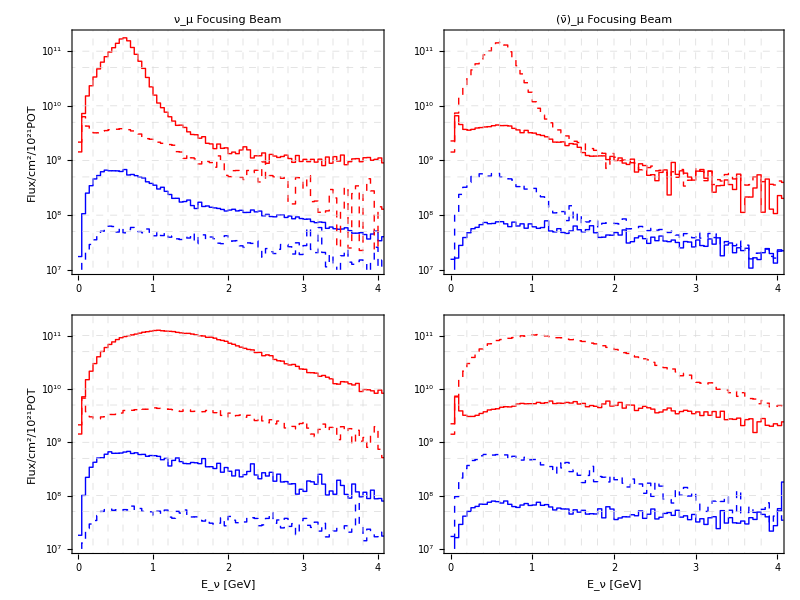

```mathematica
dir="rslt_nbeam_oab0.5";
FluxNNe05=ReadList[FileNameJoin[{workdir,dir,"data","flux_ne.dat"}],Number,RecordLists->True];
FluxNNm05=ReadList[FileNameJoin[{workdir,dir,"data","flux_nm.dat"}],Number,RecordLists->True];
FluxNAe05=ReadList[FileNameJoin[{workdir,dir,"data","flux_ae.dat"}],Number,RecordLists->True];
FluxNAm05=ReadList[FileNameJoin[{workdir,dir,"data","flux_am.dat"}],Number,RecordLists->True];
dir="rslt_nbeam_oab2.5";
FluxNNe25=ReadList[FileNameJoin[{workdir,dir,"data","flux_ne.dat"}],Number,RecordLists->True];
FluxNNm25=ReadList[FileNameJoin[{workdir,dir,"data","flux_nm.dat"}],Number,RecordLists->True];
FluxNAe25=ReadList[FileNameJoin[{workdir,dir,"data","flux_ae.dat"}],Number,RecordLists->True];
FluxNAm25=ReadList[FileNameJoin[{workdir,dir,"data","flux_am.dat"}],Number,RecordLists->True];
dir="rslt_abeam_oab0.5";
FluxANe05=ReadList[FileNameJoin[{workdir,dir,"data","flux_ne.dat"}],Number,RecordLists->True];
FluxANm05=ReadList[FileNameJoin[{workdir,dir,"data","flux_nm.dat"}],Number,RecordLists->True];
FluxAAe05=ReadList[FileNameJoin[{workdir,dir,"data","flux_ae.dat"}],Number,RecordLists->True];
FluxAAm05=ReadList[FileNameJoin[{workdir,dir,"data","flux_am.dat"}],Number,RecordLists->True];
dir="rslt_abeam_oab2.5";
FluxANe25=ReadList[FileNameJoin[{workdir,dir,"data","flux_ne.dat"}],Number,RecordLists->True];
FluxANm25=ReadList[FileNameJoin[{workdir,dir,"data","flux_nm.dat"}],Number,RecordLists->True];
FluxAAe25=ReadList[FileNameJoin[{workdir,dir,"data","flux_ae.dat"}],Number,RecordLists->True];
FluxAAm25=ReadList[FileNameJoin[{workdir,dir,"data","flux_am.dat"}],Number,RecordLists->True];

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=4;
ymin=10^7;ymax=2 10^11;
xdiv=0.2;
ydiv=ymax/10;
PlotSize=400;
TextSize=PlotSize 0.025;
TitleSize=PlotSize 0.05;
AxisLabelSize=PlotSize 0.04;
options={AspectRatio->0.5,PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}}};
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],{5 10^7,10^8,5 10^8,10^9,5 10^9,10^10,5 10^10,10^11}};

title="ν_μ Focusing Beam";
xlabel="";
ylabel="Flux/cm^2/10^21POT";
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{None,Text@Style[ylabel,AxisLabelSize]}};
FluxN25=ListLogPlotH[{FluxNNe25,FluxNNm25,FluxNAe25,FluxNAm25},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,PlotSize,{options,options1}];

xlabel="E_ν [GeV]";
ylabel="Flux/cm^2/10^21POT";
title="";
options1={PlotLabel->None,FrameLabel->{Text@Style[xlabel,AxisLabelSize],Text@Style[ylabel,AxisLabelSize]}};
FluxN05=ListLogPlotH[{FluxNNe05,FluxNNm05,FluxNAe05,FluxNAm05},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,PlotSize,{options,options1}];

title="(ν̄)_μ Focusing Beam";
xlabel="";
ylabel="";
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{None,""}};
FluxA25=ListLogPlotH[{FluxANe25,FluxANm25,FluxAAe25,FluxAAm25},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,PlotSize,{options,options1}];

title="";
xlabel="E_ν [GeV]";
options1={PlotLabel->None,FrameLabel->{Text@Style[xlabel,AxisLabelSize],""}};
FluxA05=ListLogPlotH[{FluxANe05,FluxANm05,FluxAAe05,FluxAAm05},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,PlotSize,{options,options1}];

(*Ticks->{{{0,""},{0.2,""},{0.4,""},{0.6,""},{0.8,""},{1,""},{1.2,""},{1.4,""},{1.6,""},{1.8,""},{2,""},{2.2,""},{2.4,""},{2.6,""},{2.8,""},{3,""},{3.2,""},{3.4,""},{3.6,""},{3.8,""},{4,""}},Autom}}*)

plot=Grid@Partition[{FluxN25,FluxA25,FluxN05,FluxA05},2]
Export["flux.eps",plot];
```

## Reproduction of re-evaluation paper

```mathematica
col1=1;col2=2;
PP=0;AP=5;
PlotSize=400;
TextSize=PlotSize 0.025;
TitleSize=PlotSize 0.05;
AxisLabelSize=PlotSize 0.05;
(*grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],{5 10^7,10^8,5 10^8,10^9,5 10^9,10^10,5 10^10,10^11}};*)
(*grids=Automatic;*)
xlabel="E_ν [GeV]";
ylabel="Events";
```

### π^0 momentum

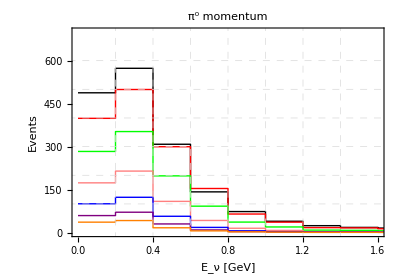

```mathematica
nb="nb";
iD="kr";
iev="pi0";
dir="rslt_nh.oab00.ppi0.noco";
oab00a=SumNu[dir,nb,iD,iev];
oab00=Multiply2Col[oab00a,1];
dir="rslt_nh.oab05.ppi0.corr2re";
oab05=SumNu[dir,nb,iD,iev];
dir="rslt_nh.oab10.ppi0.corr2re";
oab10=SumNu[dir,nb,iD,iev];
dir="rslt_nh.oab15.ppi0.corr2re";
oab15=SumNu[dir,nb,iD,iev];
dir="rslt_nh.oab20.ppi0.corr2re";
oab20=SumNu[dir,nb,iD,iev];
dir="rslt_nh.oab25.ppi0.corr2re";
oab25=SumNu[dir,nb,iD,iev];
dir="rslt_nh.oab30.ppi0.corr2re";
oab30=SumNu[dir,nb,iD,iev];

title="π^0 momentum";
ymin=0;ymax=700;
ydiv=ymax/7;
xmin=0;xmax=1.6;
xdiv=0.2;
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options={AspectRatio->0.7,PlotStyle->{Black,Red,Green,Pink,Blue,Purple,Orange}};
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{Text@Style[xlabel,AxisLabelSize],Text@Style[ylabel,AxisLabelSize]}};
ListPlotH[{oab00,oab05,oab10,oab15,oab20,oab25,oab30},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,PlotSize,{options,options1}]
```

#### Correction function of pi0 mom dist to Fig.6 in Re-evaluation paper

{aa→0.997982,b→0.0366464,c→0.624563,d→0.357516,e→0.112417}

Function[{x},-0.357516 ⅇ^(-22.2222 (-1.29+x)^2)+0.624563 ⅇ^(-138.889 (-0.7+x)^2)-0.112417 ⅇ^(-12.5 (-0.5+x)^2)+0.997982 ⅇ^(-0.0366464 x)]

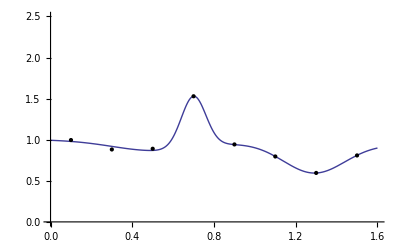

```mathematica
nb="nb";
iD="kr";
iev="pi0";
dir="rslt_nh.oab00.ppi0";
oab00=SumNu[dir,nb,iD,iev];
oab00re={{0.1,450},{0.3,550},{0.5,350},{0.7,160},{0.9,80},{1.1,40},{1.3,21},{1.5,18}};
tmp=Table[oab00re[[i,2]],{i,1,Length[oab00re]}];
renoab00re=Norm2Col[oab00re];
oab002=Table[{oab00[[i,1]]+0.1,oab00[[i,2]]},{i,1,8}];
renoab002=Norm2Col[oab002];
ratio2=Table[{renoab002[[i,1]],renoab00re[[i,2]]/renoab002[[i,2]]},{i,1,8}];
ratiocorr={0.92,0.9,0.95,1.2,1,1,1,1};
ratio=Table[{ratio2[[i,1]],ratio2[[i,2]] ratiocorr[[i]]},{i,1,8}];
Pdata=ListPlot[ratio];
model=aa Exp[-b x]+c Exp[-(x-0.7)^2/(2 0.06^2)]-d Exp[-(x-1.29)^2/(2 0.15^2)]-e Exp[-(x-0.5)^2/(2 0.2^2)];
fit=FindFit[ratio,model,{aa,b,c,d,e},x]
modelf=Function[{x},Evaluate[model/.fit]]
Plot[modelf[x],{x,0,1.6},Epilog->Map[Point,ratio],PlotRange->{{0,1.6},{0,2.5}}]
```

```mathematica
modelf[0.7]
```

11.7802

### Typical event numbers

#### Definitions

```mathematica
ErecDistElike[qedir_,resdir_,iD_,nb_,titleAdd_,Size_,ymax_,idiv_]:=Module[{TextSize,TitleSize,AxisLabelSize,xlabel,ylabel,xmin,xmax,xdiv,iev,QEE2e,QEM2e,ResE2e,ResM2e,E2e,M2e,pi0,gam,Elike,ymin,plike,grids,ydiv,options,options1,title},

iev="e2e";
QEE2e=SumNu[qedir,nb,iD,iev];
iev="m2e";
QEM2e=SumNu[qedir,nb,iD,iev];
iev="e2e";
ResE2e=SumNu[resdir,nb,iD,iev];
iev="m2e";
ResM2e=SumNu[resdir,nb,iD,iev];
E2e=Sum2Col[QEE2e,ResE2e];
M2e=Sum2Col[QEM2e,ResM2e];
iev="pi0";
pi0=SumNu[qedir,nb,iD,iev];
iev="gam";
gam=SumNu[qedir,nb,iD,iev];
Elike=Sum2Col[E2e,M2e];Elike=Sum2Col[Elike,pi0];Elike=Sum2Col[Elike,gam];

title="e-like events"<>titleAdd;
TextSize=Size 0.025;
TitleSize=Size 0.05;
AxisLabelSize=Size 0.05;
xlabel="E_rec [GeV]";
ylabel="Events";
xmin=0.4;xmax=3;xdiv=0.2;
ymin=0;ydiv=ymax/idiv;
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymaxE/ydiv]-1}]};
options={AspectRatio->0.7,PlotStyle->{Black,Blue,Green,Red,Purple}};
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{Text@Style[xlabel,AxisLabelSize],Text@Style[ylabel,AxisLabelSize]}};
plike=ListPlotH[{Elike,QEE2e,ResE2e,pi0,M2e,gam},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,Size,{options,options1}];
Return[plike];
]

ErecDistMulike[qedir_,resdir_,iD_,nb_,titleAdd_,Size_,ymax_,idiv_]:=Module[{TextSize,TitleSize,AxisLabelSize,xlabel,ylabel,xmin,xmax,xdiv,iev,QEE2m,QEM2m,ResE2m,ResM2m,E2m,M2m,Mulike,ymin,plike,grids,ydiv,options,options1,title},

iev="e2m";
QEE2m=SumNu[qedir,nb,iD,iev];
iev="m2m";
QEM2m=SumNu[qedir,nb,iD,iev];
iev="e2m";
ResE2m=SumNu[resdir,nb,iD,iev];
iev="m2m";
ResM2m=SumNu[resdir,nb,iD,iev];
E2m=Sum2Col[QEE2m,ResE2m];
M2m=Sum2Col[QEM2m,ResM2m];
Mulike=Sum2Col[E2m,M2m];

title="μ-like events"<>titleAdd;
TextSize=Size 0.025;
TitleSize=Size 0.05;
AxisLabelSize=Size 0.05;
xlabel="E_rec [GeV]";
ylabel="Events";
xmin=0.4;xmax=3;xdiv=0.2;
ymin=0;ydiv=ymax/idiv;
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymaxE/ydiv]-1}]};
options={AspectRatio->0.7,PlotStyle->{Black,Blue,Green,Purple}};
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{Text@Style[xlabel,AxisLabelSize],Text@Style[ylabel,AxisLabelSize]}};
plike=ListPlotH[{Mulike,QEM2m,ResM2m,E2m},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,Size,{options,options1}];
Return[plike];
]

ErecDist[qedir_,resdir_,nb_,iD_,titleAdd_,Size_,ymaxE_,idivE_,ymaxMu_,idivMu_]:=Module[{QEE2e,iev,QEM2e,ResE2e,ResM2e,E2e,M2e,pi0,gam,Elike,QEE2m,QEM2m,ResE2m,ResM2m,E2m,M2m,Mulike,titleMu,ydiv,grids,options,options1,pElike,pMulike,titleE,ymin,col1,PP,PlotSize,TextSize,TitleSize,AxisLabelSize,xlabel,ylabel,xmin,xmax,xdiv,col2,AP},
pElike=ErecDistElike[qedir,resdir,iD,nb,titleAdd,Size,ymaxE,idivE];
pMulike=ErecDistMulike[qedir,resdir,iD,nb,titleAdd,Size,ymaxMu,idivMu];
Return[Grid@Partition[{pMulike,pElike},2]];
]

ErecDetector[iD_,Det_,DirAppQE_,DirAppRes_,Size_,ymaxE_,idivE_,ymaxMu_,idivMu_]:=Module[{nb,MH,qedir,resdir,SkNbNh,SkNbIh,SkAbNh,SkAbIh},
nb="nb";
MH="nh";
qedir="rslt_"<>MH<>DirAppQE;
resdir="rslt_"<>MH<>DirAppRes;
SkNbNh=ErecDist[qedir,resdir,nb,iD,": ν beam NH ("<>Det<>")",Size,ymaxE,idivE,ymaxMu,idivMu];
MH="ih";
qedir="rslt_"<>MH<>DirAppQE;
resdir="rslt_"<>MH<>DirAppRes;
SkNbIh=ErecDist[qedir,resdir,nb,iD,": ν beam IH ("<>Det<>")",Size,ymaxE,idivE,ymaxMu,idivMu];
nb="ab";
MH="nh";
qedir="rslt_"<>MH<>DirAppQE;
resdir="rslt_"<>MH<>DirAppRes;
SkAbNh=ErecDist[qedir,resdir,nb,iD,": ν̄ beam NH ("<>Det<>")",Size,ymaxE,idivE,ymaxMu,idivMu];
MH="ih";
qedir="rslt_"<>MH<>DirAppQE;
resdir="rslt_"<>MH<>DirAppRes;
SkAbIh=ErecDist[qedir,resdir,nb,iD,": ν̄ beam IH ("<>Det<>")",Size,ymaxE,idivE,ymaxMu,idivMu];
Return[Grid@Partition[{SkNbNh,SkAbNh,SkNbIh,SkAbIh},2]]
]
```

#### Plots

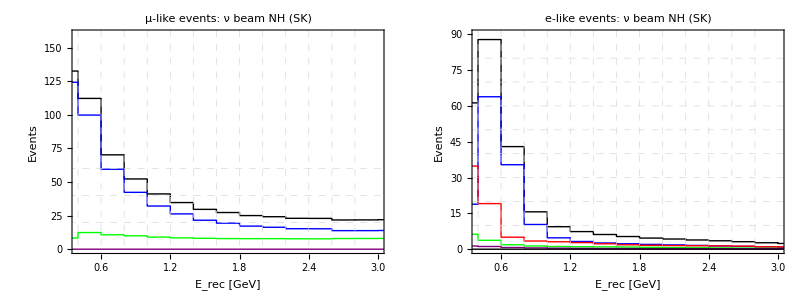
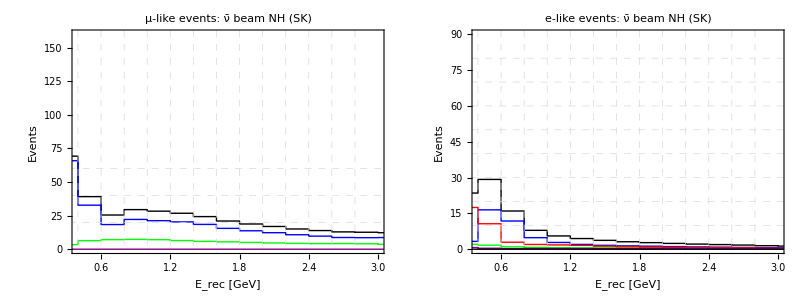
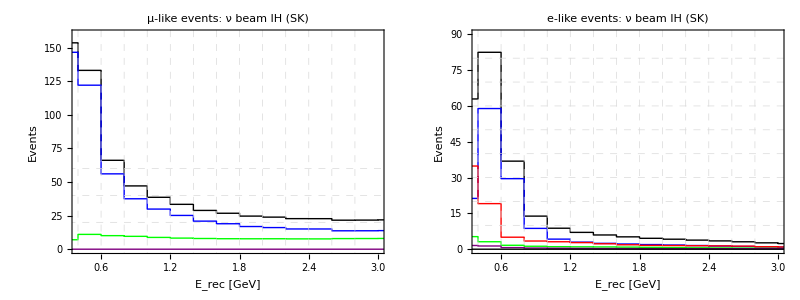
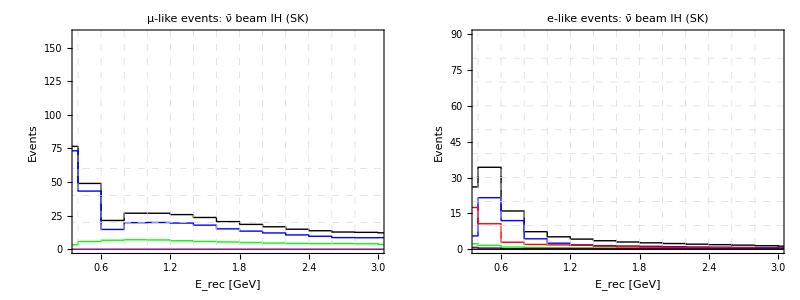
-Graphics- | -Graphics-
-Graphics- | -Graphics-

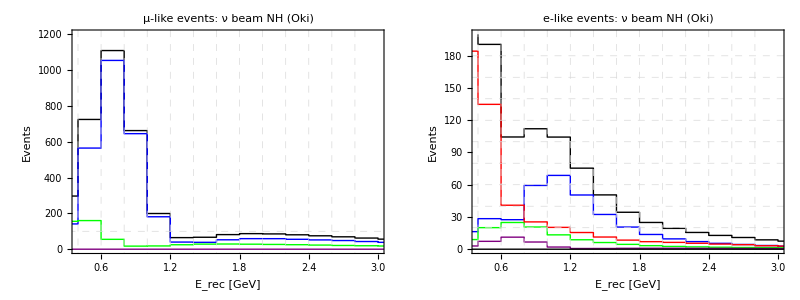
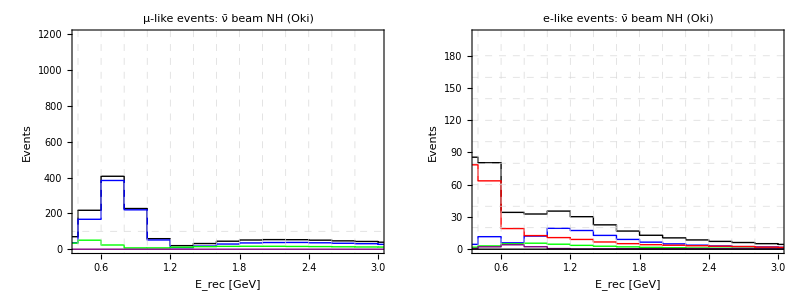
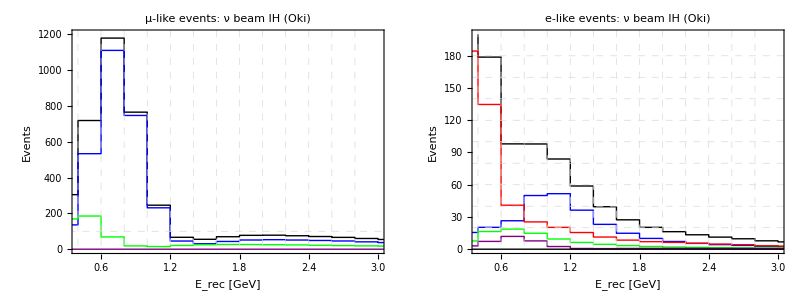
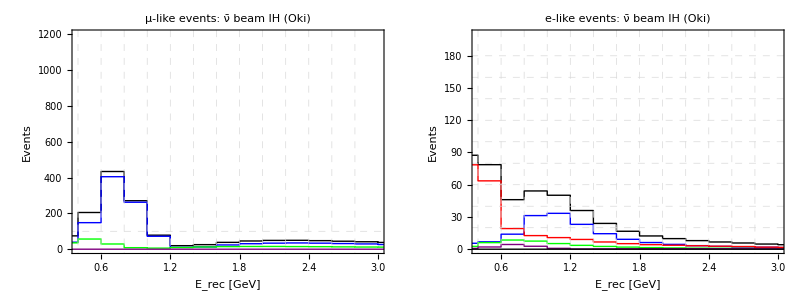
-Graphics- | -Graphics-
-Graphics- | -Graphics-

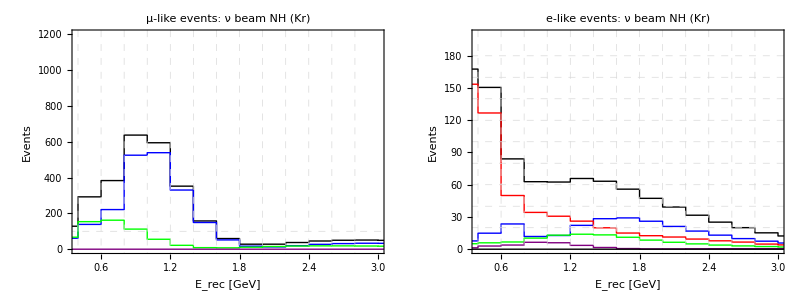
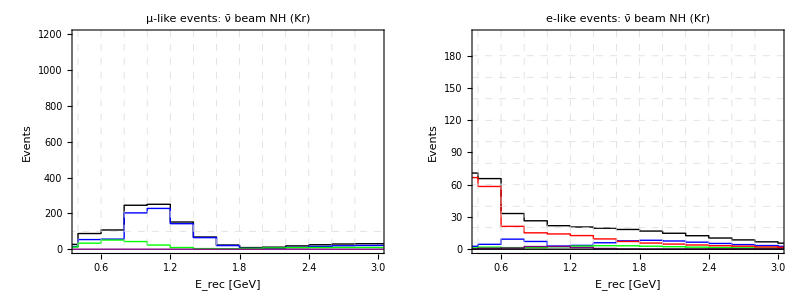
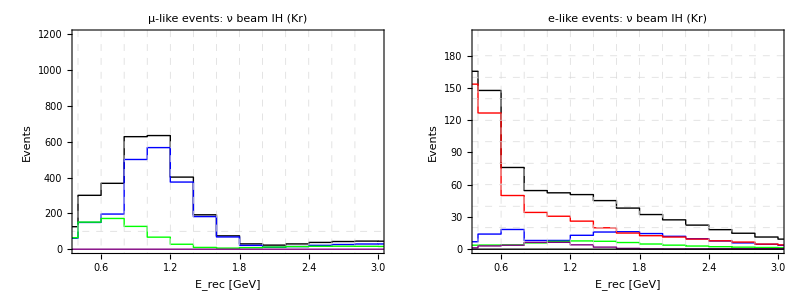
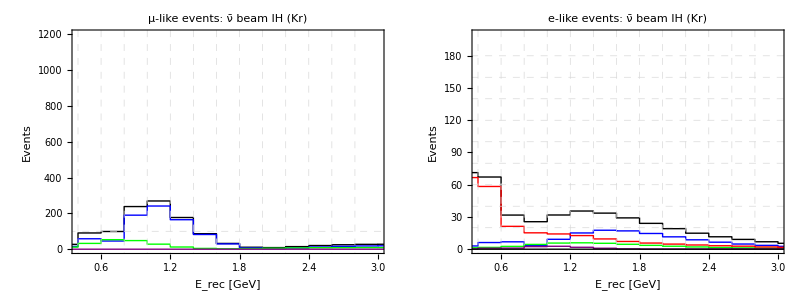
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(*DirAppQE=".qe.old.noco";*)
DirAppQE=".qe.old";
(*DirAppQE=".qe";*)
(*DirAppRes=".res.old.noco";*)
DirAppRes=".res.old";
(*DirAppRes=".res";*)

PlotSize=300;
ymaxE=90;ydivE=9;ymaxMu=160;ydivMu=8;
ErecDetector["sk","SK",DirAppQE,DirAppRes,PlotSize,ymaxE,ydivE,ymaxMu,ydivMu]
ymaxE=200;ydivE=10;ymaxMu=1200;ydivMu=12;
ErecDetector["oki","Oki",DirAppQE,DirAppRes,PlotSize,ymaxE,ydivE,ymaxMu,ydivMu]
ErecDetector["kr","Kr",DirAppQE,DirAppRes,PlotSize,ymaxE,ydivE,ymaxMu,ydivMu]
```

## Reproduction of Oki paper

### Typical event numbers

```mathematica
col1=1;col2=2;
PP=0;AP=5;
xmin=0.4;xmax=3;
xdiv=0.2;
PlotSize=400;
TextSize=PlotSize 0.025;
TitleSize=PlotSize 0.05;
AxisLabelSize=PlotSize 0.05;
(*grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],{5 10^7,10^8,5 10^8,10^9,5 10^9,10^10,5 10^10,10^11}};*)
(*grids=Automatic;*)
xlabel="E_ν [GeV]";
ylabel="Events";
```

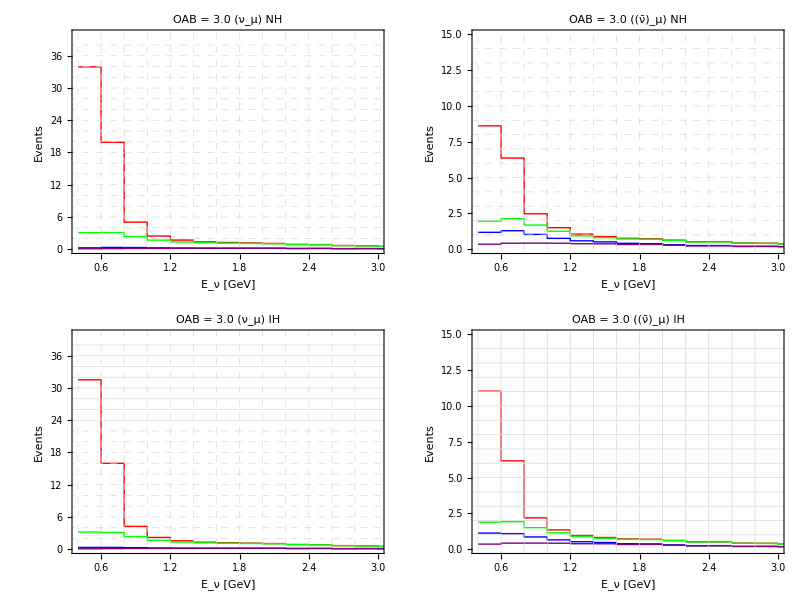

```mathematica
iD="sk";
dir="rslt_nh.oab30";
NbNeNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_nb."<>iD<>".ne.ne.e.dat"}],Number,RecordLists->True];
NbNmNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_nb."<>iD<>".nm.ne.e.dat"}],Number,RecordLists->True];
NbAeAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_nb."<>iD<>".ae.ae.e.dat"}],Number,RecordLists->True];
NbAmAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_nb."<>iD<>".am.ae.e.dat"}],Number,RecordLists->True];
AbNeNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_ab."<>iD<>".ne.ne.e.dat"}],Number,RecordLists->True];
AbNmNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_ab."<>iD<>".nm.ne.e.dat"}],Number,RecordLists->True];
AbAeAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_ab."<>iD<>".ae.ae.e.dat"}],Number,RecordLists->True];
AbAmAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_ab."<>iD<>".am.ae.e.dat"}],Number,RecordLists->True];

NbAe=Table[{NbNeNe[[i,1]],NbAmAe[[i,2]]+NbAeAe[[i,2]]},{i,1,Length[NbNeNe]}];
NbBG=Table[{NbNeNe[[i,1]],NbNeNe[[i,2]]+NbAe[[i,2]]},{i,1,Length[NbNeNe]}];
Nbe=Table[{NbNeNe[[i,1]],NbNmNe[[i,2]]+NbBG[[i,2]]},{i,1,Length[NbNeNe]}];
AbNe=Table[{NbNeNe[[i,1]],AbNmNe[[i,2]]+AbNeNe[[i,2]]},{i,1,Length[NbNeNe]}];
AbBG=Table[{NbNeNe[[i,1]],AbAeAe[[i,2]]+AbNe[[i,2]]},{i,1,Length[NbNeNe]}];
Abe=Table[{NbNeNe[[i,1]],AbAmAe[[i,2]]+AbBG[[i,2]]},{i,1,Length[NbNeNe]}];

title="OAB = 3.0 (ν_μ) NH";
ymin=0;ymax=40;
ydiv=ymax/20;
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options={AspectRatio->0.7,PlotStyle->{Red,Green,Blue,Purple}};
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{Text@Style[xlabel,AxisLabelSize],Text@Style[ylabel,AxisLabelSize]}};
NHNb=ListPlotH[{Nbe,NbBG,NbAe,NbAeAe},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,PlotSize,{options,options1}];
title="OAB = 3.0 ((ν̄)_μ) NH";
ymin=0;ymax=15;
ydiv=ymax/15;
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options={AspectRatio->0.7,PlotStyle->{Red,Green,Blue,Purple}};
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{Text@Style[xlabel,AxisLabelSize],Text@Style[ylabel,AxisLabelSize]}};
NHAb=ListPlotH[{Abe,AbBG,AbNe,AbNeNe},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,PlotSize,{options,options1}];

dir="rslt_ih.oab30";
NbNeNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_nb."<>iD<>".ne.ne.e.dat"}],Number,RecordLists->True];
NbNmNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_nb."<>iD<>".nm.ne.e.dat"}],Number,RecordLists->True];
NbAeAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_nb."<>iD<>".ae.ae.e.dat"}],Number,RecordLists->True];
NbAmAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_nb."<>iD<>".am.ae.e.dat"}],Number,RecordLists->True];
AbNeNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_ab."<>iD<>".ne.ne.e.dat"}],Number,RecordLists->True];
AbNmNe=ReadList[FileNameJoin[{workdir,dir,"data","dat_ab."<>iD<>".nm.ne.e.dat"}],Number,RecordLists->True];
AbAeAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_ab."<>iD<>".ae.ae.e.dat"}],Number,RecordLists->True];
AbAmAe=ReadList[FileNameJoin[{workdir,dir,"data","dat_ab."<>iD<>".am.ae.e.dat"}],Number,RecordLists->True];

NbAe=Table[{NbNeNe[[i,1]],NbAmAe[[i,2]]+NbAeAe[[i,2]]},{i,1,Length[NbNeNe]}];
NbBG=Table[{NbNeNe[[i,1]],NbNeNe[[i,2]]+NbAe[[i,2]]},{i,1,Length[NbNeNe]}];
Nbe=Table[{NbNeNe[[i,1]],NbNmNe[[i,2]]+NbBG[[i,2]]},{i,1,Length[NbNeNe]}];
AbNe=Table[{NbNeNe[[i,1]],AbNmNe[[i,2]]+AbNeNe[[i,2]]},{i,1,Length[NbNeNe]}];
AbBG=Table[{NbNeNe[[i,1]],AbAeAe[[i,2]]+AbNe[[i,2]]},{i,1,Length[NbNeNe]}];
Abe=Table[{NbNeNe[[i,1]],AbAmAe[[i,2]]+AbBG[[i,2]]},{i,1,Length[NbNeNe]}];

title="OAB = 3.0 (ν_μ) IH";
ymin=0;ymax=40;
ydiv=ymax/20;
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options={AspectRatio->0.7,PlotStyle->{Red,Green,Blue,Purple}};
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{Text@Style[xlabel,AxisLabelSize],Text@Style[ylabel,AxisLabelSize]}};
IHNb=ListPlotH[{Nbe,NbBG,NbAe,NbAeAe},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,PlotSize,{options,options1}];
title="OAB = 3.0 ((ν̄)_μ) IH";
ymin=0;ymax=15;
ydiv=ymax/15;
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options={AspectRatio->0.7,PlotStyle->{Red,Green,Blue,Purple}};
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{Text@Style[xlabel,AxisLabelSize],Text@Style[ylabel,AxisLabelSize]}};
IHAb=ListPlotH[{Abe,AbBG,AbNe,AbNeNe},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,PlotSize,{options,options1}];

Grid@Partition[{NHNb,NHAb,IHNb,IHAb},2]
```

## NC π^0 uncertainty

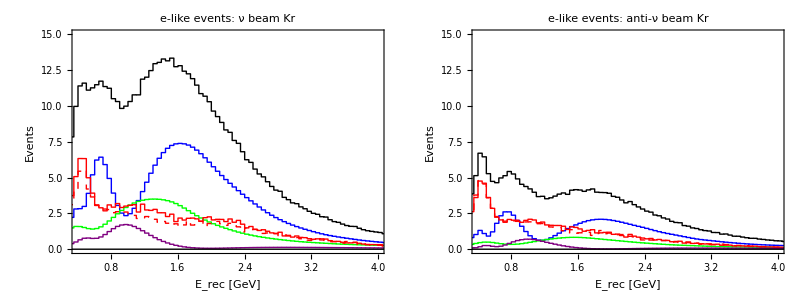

```mathematica
Size=400;
MH="nh";
DirAppQE=".qe.50";
DirAppRes=".res.50";
qedir="rslt_"<>MH<>DirAppQE;
resdir="rslt_"<>MH<>DirAppRes;

nb="nb";
iD="kr";
iev="e2e";
QEE2e=SumNu[qedir,nb,iD,iev];
iev="m2e";
QEM2e=SumNu[qedir,nb,iD,iev];
iev="e2e";
ResE2e=SumNu[resdir,nb,iD,iev];
iev="m2e";
ResM2e=SumNu[resdir,nb,iD,iev];
E2e=Sum2Col[QEE2e,ResE2e];
M2e=Sum2Col[QEM2e,ResM2e];
iev="pi0";
pi0dir="rslt_pi0.t2k.50";
pi0Mean=SumNu[pi0dir,nb,iD,iev];
pi0dir="rslt_pi0.lowmaco.50";
pi0Low=SumNu[pi0dir,nb,iD,iev];
iev="gam";
gam=SumNu[qedir,nb,iD,iev];
Elike=Sum2Col[E2e,M2e];Elike=Sum2Col[Elike,pi0Mean];Elike=Sum2Col[Elike,gam];

title="e-like events: ν beam Kr";
TextSize=Size 0.025;
TitleSize=Size 0.05;
AxisLabelSize=Size 0.05;
xlabel="E_rec [GeV]";
ylabel="Events";
xmin=0.4;xmax=4;xdiv=0.2;
ymin=0;ymax=15;ydiv=ymax/8;
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options={AspectRatio->0.7,PlotStyle->{Black,Blue,Green,Red,{Red,Dashed},Purple}};
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{Text@Style[xlabel,AxisLabelSize],Text@Style[ylabel,AxisLabelSize]}};
plike1=ListPlotH[{Elike,QEE2e,ResE2e,pi0Mean,pi0Low,M2e,gam},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,Size,{options,options1}];

nb="ab";
iD="kr";
iev="e2e";
QEE2e=SumNu[qedir,nb,iD,iev];
iev="m2e";
QEM2e=SumNu[qedir,nb,iD,iev];
iev="e2e";
ResE2e=SumNu[resdir,nb,iD,iev];
iev="m2e";
ResM2e=SumNu[resdir,nb,iD,iev];
E2e=Sum2Col[QEE2e,ResE2e];
M2e=Sum2Col[QEM2e,ResM2e];
iev="pi0";
pi0dir="rslt_pi0.t2k.50";
pi0Mean=SumNu[pi0dir,nb,iD,iev];
pi0dir="rslt_pi0.lowmaco.50";
pi0Low=SumNu[pi0dir,nb,iD,iev];
iev="gam";
gam=SumNu[qedir,nb,iD,iev];
Elike=Sum2Col[E2e,M2e];Elike=Sum2Col[Elike,pi0Mean];Elike=Sum2Col[Elike,gam];

title="e-like events: ν̄ beam Kr" ;
TextSize=Size 0.025;
TitleSize=Size 0.05;
AxisLabelSize=Size 0.05;
xlabel="E_rec [GeV]";
ylabel="Events";
xmin=0.4;xmax=4;xdiv=0.2;
ymin=0;ymax=15;ydiv=ymax/8;
grids={Table[xdiv i,{i,Floor[xmax/xdiv]-1}],Table[ydiv i,{i,Floor[ymax/ydiv]-1}]};
options={AspectRatio->0.7,PlotStyle->{Black,Blue,Green,Red,{Red,Dashed},Purple}};
options1={PlotLabel->Text@Style[title,TitleSize],FrameLabel->{Text@Style[xlabel,AxisLabelSize],Text@Style[ylabel,AxisLabelSize]}};
plike2=ListPlotH[{Elike,QEE2e,ResE2e,pi0Mean,pi0Low,M2e,gam},title,xlabel,ylabel,xmin,xmax,ymin,ymax,grids,Size,{options,options1}];

Grid@Partition[{plike1,plike2},2]
```

## archive

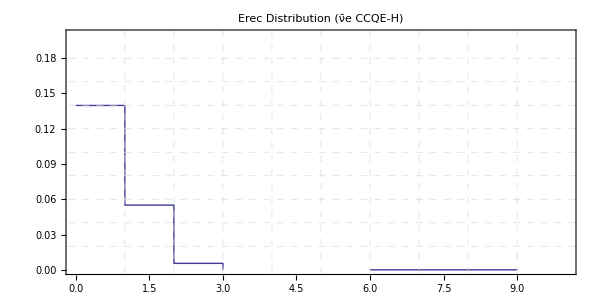

```mathematica
x=5;
r1=1;
sig1=268( Exp[-0.0225 x]-Exp[-0.135 x -0.047]);
dE1=18.3/(1+34Exp[-1.02x]);
r2=4.47(Exp[0.114x-2.59]-Exp[-0.698x-2.36]);
sig2=297(1-Exp[-0.235 x]);
dE2=-7.26-5.66x;
r3=0.00532Exp[0.620x];
sig3=4.41(Exp[0.0584x+4.27]-Exp[-0.489x+4.47]);
dE3=665(Exp[-0.261x+0.0811]-Exp[-0.107x]);
x2=1000x;
aeCCQEH[y_]:=If[x2≤1000,r1 Exp[-(y 1000-x2+dE1)^2/(2 sig1^2)]+r2 Exp[-(y 1000-x2+dE2)^2/(2 sig2^2)],r1 Exp[-(y 1000-x2+dE1)^2/(2 sig1^2)]+r2 Exp[-(y 1000-x2+dE2)^2/(2 sig2^2)]+r3 Exp[-(y 1000-x2+dE3)^2/(2 sig3^2)]]

test=ReadList[FileNameJoin[{workdir,"beam_neu_conv/","rslt_test","data","test_data.dat"}],Number,RecordLists->True];
col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=10;
ymin=0;ymax=0.2;
xdiv=xmax/10;
ydiv=ymax/10;
title="Erec Distribution (ν̄e CCQE-H)";
options={AspectRatio->0.5,ImageSize->600(*,PlotStyle->Blue*)};
ListPlotHG[{test},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

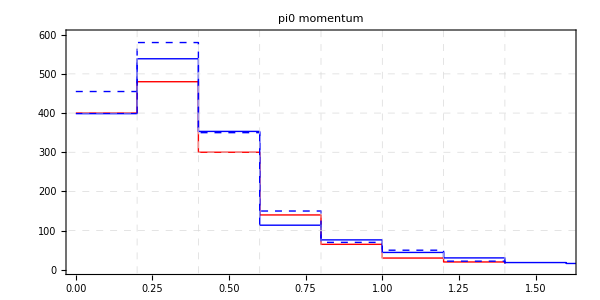

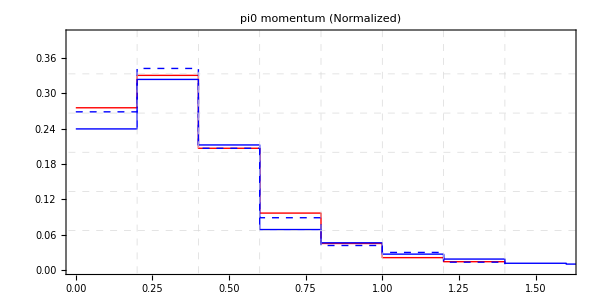

```mathematica
paw={{0,455.},{0.2,580},{0.4,350},{0.6,150},{0.8,70},{1.0,50},{1.2,22},{1.4,16}};
okamura={{0,400},{0.2,480},{0.4,300},{0.6,140},{0.8,65},{1.0,30},{1.2,20},{1.4,16}};
paw2=#[[2]]&/@paw;
paw3={#[[1]],#[[2]]/Total[paw2]}&/@paw;
okamura2=#[[2]]&/@okamura;
okamura3={#[[1]],#[[2]]/Total[okamura2]}&/@okamura;
pi0bg2=#[[2]]&/@pi0bg;
pi0bg3={#[[1]],#[[2]]/Total[pi0bg2]}&/@pi0bg;

col1=1;col2=2;
PP=0;AP=4;
xmin=0;xmax=1.6;
ymin=0;ymax=600;
xdiv=xmax/8;
ydiv=ymax/6;
title="pi0 momentum";
options={AspectRatio->0.5,ImageSize->600,PlotStyle->{Red,Blue,{Blue,Dashed}}(*,PlotStyle->Blue*)};
ListPlotHG[{okamura,pi0bg,paw},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
xmin=0;xmax=1.6;
ymin=0;ymax=0.4;
xdiv=xmax/8;
ydiv=ymax/6;
title="pi0 momentum (Normalized)";
options={AspectRatio->0.5,ImageSize->600,PlotStyle->{Red,Blue,{Blue,Dashed}}(*,PlotStyle->Blue*)};
ListPlotHG[{okamura3,pi0bg3,paw3},title,xmin,xmax,ymin,ymax,xdiv,ydiv,options]
```

```mathematica
37/60.
```

0.616667